```mathematica
SetOptions[$FrontEnd,"CommonDefaultFormatTypes"->{"Output"->StandardForm}]
basepath=$HomeDirectory<>"/sivers_TMD_PhD_project/mathematica_hari"
SetDirectory[basepath<>"/output"];
includepath=basepath<>"/include";
AppendTo[$Path, includepath];
Needs["LatticeAnalysis`"];
 <<"LatticeAnalysis`"
(* do not keep track of intermediate results *)
$HistoryLength=0;
Needs["FourierSeries`"]
lata=0.11403
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/mathematica_hari

0.11403

## Open Database

```mathematica
AmpDB = BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/newDBforA12BA2B/db_Alleta_correct_try_A12B_A2B_bL_bT_bevenodd.bidatex"]
(*AmpDBPbbsq = BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/newDBforA12BA2B/db_Alleta_correct_try_A12B_A2B_Pb32by2Pi_bsq_bevenodd.bidatex"]*)
```

< -MemDB- {A,bL,bNum,bT,data,EN,etav,MN,PL,zta}>

```mathematica
modelfitJackkife[model_, fitParams_, x_, y_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,y,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
modelfitJackkifefor4D[model_,fitParams_,x_,y_,z_]:=Module[{numFs,modelvaluej,modelvalue,jackknifeResults, numParams},numFs=Length[fitParams[[1]]];
numParams=Length[fitParams];
modelvaluej[j_]:=Module[{datafitParams},datafitParams=Table[fitParams[[k,j]],{k,numParams}];
model[x,y,z,datafitParams]];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@modelvalue;
jackknifeResults];
meanfromJK[JKvalue_]:=Module[{meanvalue},
meanvalue = MakeErrBars[{{1,JKvalue}}][[1]][[1]][[2]];
meanvalue
];
errorfromJK[JKvalue_]:=Module[{errorvalue},
errorvalue = MakeErrBars[{{1,JKvalue}}][[1]][[2]][[1]][[2]];
errorvalue
];
chisqOEsigmasq[O_, E_]:=Module[{OEsigmasq, Omean,Emean, Esigmasq, Osigmasq, sigmasqTotal},
Omean=meanfromJK[O];
Emean=meanfromJK[E];
Esigmasq = (MakeErrBars[{{1,E}}][[1]][[2]][[1]][[2]])^2;
Osigmasq = (MakeErrBars[{{1,O}}][[1]][[2]][[1]][[2]])^2;
sigmasqTotal = Esigmasq+Osigmasq;
OEsigmasq = If[sigmasqTotal==0,0,((Omean-Emean)^2)/sigmasqTotal];
OEsigmasq
];

JackknifeFit3D[xyJKf_,model_,para_,vari_, modelFnName_]:=Module[
{numFs,fitParamsForFj,fitParamsList,paramLists,jackknifeResults,DoF, chisquare, observed, expected, chisquareperDoF},
numFs=Length[xyJKf[[1,3]]];
(*Function to extract j-th f values and fit them*)
fitParamsForFj[j_]:=Module[{data,fit},
data={#[[1]],#[[2]],#[[3,j]]}&/@xyJKf;(*Extract f_j values*)
fit=NonlinearModelFit[data,model,para,vari];
fit["BestFitParameters"] (*Extract fitted parameters*)
];
(*Compute fit parameters for each f_j*)
fitParamsList=Table[fitParamsForFj[j],{j,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
DoF=Length[xyJKf];
chisquare=0;
Do[
observed = modelfitJackkife[modelFnName, jackknifeResults, xyJKf[[i]][[1]], xyJKf[[i]][[2]]];
expected= xyJKf[[i]][[3]];
chisquare = chisquare + chisqOEsigmasq[observed, expected];
,{i,DoF}];
chisquareperDoF=chisquare/(DoF-3);
{FitParameters->jackknifeResults, chisquareDoF->chisquareperDoF}];

JackknifeFit4D[nxyJKf_,model_,para_,vari_,modelFnName_,init_:Automatic]:=Module[{numFs,fitParamsForFj,fitParamsList,jackknifeResults,DoF,chisquare,observed,expected,chisquareperDoF},numFs=Length[nxyJKf[[1,4]]];
WeightList=Table[With[{σ=MakeErrBars[{{1,nxyJKf[[ii,4]]}}][[1,2,1,2]]},1/Max[σ,10^-6]^2],{ii,Length[nxyJKf]}];
fitParamsForFj[j_]:=Module[{data,fit},data={#[[1]],#[[2]],#[[3]],#[[4,j]]}&/@nxyJKf;
fit=NonlinearModelFit[data,model,If[init===Automatic,para,init],vari, Weights->WeightList,Method->{"LevenbergMarquardt"}];
fit["BestFitParameters"]];
fitParamsList=Table[fitParamsForFj[j],{j,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
jackknifeResults = jackknifeResults[[All,All, 1]];
DoF=Length[nxyJKf];
chisquare=Total[Table[observed=modelfitJackkifefor4D[modelFnName,jackknifeResults,nxyJKf[[i,1]],nxyJKf[[i,2]],nxyJKf[[i,3]]];
expected=nxyJKf[[i,4]];
chisqOEsigmasq[observed,expected],{i,DoF}]];
chisquareperDoF=chisquare/(DoF-Length[para]);
{FitParameters->jackknifeResults,chisquareDoF->chisquareperDoF}];

JackknifeFit4DGaussianCons[nxyJKf_,model_,para_,vari_,modelFnName_,init_:Automatic]:=Module[{numFs,fitParamsForFj,fitParamsList,jackknifeResults,DoF,chisquare,observed,expected,chisquareperDoF},numFs=Length[nxyJKf[[1,4]]];
WeightList=Table[With[{σ=MakeErrBars[{{1,nxyJKf[[ii,4]]}}][[1,2,1,2]]},1/Max[σ,10^-6]^2],{ii,Length[nxyJKf]}];
fitParamsForFj[j_]:=Module[{data,fit},data={#[[1]],#[[2]],#[[3]],#[[4,j]]}&/@nxyJKf;
fit=NonlinearModelFit[data,{model, c>0.09},If[init===Automatic,para,init],vari,Weights->WeightList];
fit["BestFitParameters"]];
fitParamsList=Table[fitParamsForFj[j],{j,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
jackknifeResults = jackknifeResults[[All,All, 1]];
DoF=Length[nxyJKf];
chisquare=Total[Table[observed=modelfitJackkifefor4D[modelFnName,jackknifeResults,nxyJKf[[i,1]],nxyJKf[[i,2]],nxyJKf[[i,3]]];
expected=nxyJKf[[i,4]];
chisqOEsigmasq[observed,expected],{i,DoF}]];
chisquareperDoF=chisquare/(DoF-Length[para]);
{FitParameters->jackknifeResults,chisquareDoF->chisquareperDoF}];

modelfitJackkifband[model_, fitParams_,fixedVare_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x, fixedVare,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];


modelfitJackkifex[model_, fitParams_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
modelfitJackkifex[model_, fitParams_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
```

```mathematica
modelfitJackkifex[model_, fitParams_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]],fitParams[[4]][[j]]};
model[x,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];

modelJackk[model_, fitParam_, multipliar_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParam];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams=fitParam[[j]];
model[datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults*multipliar
];
PowerJackk[a_,b_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[b];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams=(a)^b[[j]];
datafitParams
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
ExpJackk[b_,eta_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[b];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams=Exp[b[[j]]*eta];
datafitParams
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
```

```mathematica
(* =========================================================================*)(*Optimized Helper Functions for Jackknife& Chi-Square*)(* =========================================================================*)modelfitJackkife[model_,fitParams_,x_,y_]:=JacknifeSamples@@(model[x,y,#]&/@Transpose[List@@@fitParams]);

modelfitJackkifefor4D[model_,fitParams_,x_,y_,z_]:=JacknifeSamples@@(model[x,y,z,#]&/@Transpose[List@@@fitParams]);

meanfromJK[JKvalue_]:=MakeErrBars[{{1,JKvalue}}][[1,1,2]];
errorfromJK[JKvalue_]:=MakeErrBars[{{1,JKvalue}}][[1,2,1,2]];

chisqOEsigmasq[O_,E_]:=Module[{Omean,Emean,Esigmasq,Osigmasq,sigmasqTotal},Omean=meanfromJK[O];
Emean=meanfromJK[E];
Esigmasq=errorfromJK[E]^2;
Osigmasq=errorfromJK[O]^2;
sigmasqTotal=Esigmasq+Osigmasq;
If[sigmasqTotal==0,0,(Omean-Emean)^2/sigmasqTotal]];

JackknifeFit3D[xyJKf_,model_,para_,vari_,modelFnName_]:=Module[{numFs,fitParamsForFj,fitParamsList,jackknifeResults,DoF,chisquare,observed,expected,chisquareperDoF},numFs=Length[xyJKf[[1,3]]];
(*Renamed loop variable to jkIndex to prevent collisions with parameter'j'*)fitParamsForFj[jkIndex_]:=Module[{data,fit},data={#[[1]],#[[2]],#[[3,jkIndex]]}&/@xyJKf;
fit=NonlinearModelFit[data,model,para,vari];
fit["BestFitParameters"]];
fitParamsList=Table[fitParamsForFj[jkIndex],{jkIndex,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
DoF=Length[xyJKf];
chisquare=Total[Map[Function[pt,observed=modelfitJackkife[modelFnName,jackknifeResults,pt[[1]],pt[[2]]];
chisqOEsigmasq[observed,pt[[3]]]],xyJKf]];
chisquareperDoF=chisquare/(DoF-3);
{FitParameters->jackknifeResults,chisquareDoF->chisquareperDoF}];

JackknifeFit4D[nxyJKf_,model_,para_,vari_,modelFnName_,init_:Automatic]:=Module[{numFs,fitParamsForFj,fitParamsList,jackknifeResults,DoF,chisquare,observed,expected,chisquareperDoF,WeightList},numFs=Length[nxyJKf[[1,4]]];
WeightList=(1/Max[errorfromJK[#[[4]]],10^-6]^2)&/@nxyJKf;
(*Renamed loop variable to jkIndex to prevent collisions with parameter'j'*)fitParamsForFj[jkIndex_]:=Module[{data,fit},data={#[[1]],#[[2]],#[[3]],#[[4,jkIndex]]}&/@nxyJKf;
fit=NonlinearModelFit[data,model,If[init===Automatic,para,init],vari,Weights->WeightList,Method->{"LevenbergMarquardt"}];
fit["BestFitParameters"]];
fitParamsList=Table[fitParamsForFj[jkIndex],{jkIndex,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
jackknifeResults=jackknifeResults[[All,All,1]];
DoF=Length[nxyJKf];
chisquare=Total[Map[Function[pt,observed=modelfitJackkifefor4D[modelFnName,jackknifeResults,pt[[1]],pt[[2]],pt[[3]]];
chisqOEsigmasq[observed,pt[[4]]]],nxyJKf]];
chisquareperDoF=chisquare/(DoF-Length[para]);
{FitParameters->jackknifeResults,chisquareDoF->chisquareperDoF}];
```

```mathematica
(* =========================================================================*)(*4D Global Fits for ReA2B (Exponential in P.b)*)(* =========================================================================*)FitetarangeList[bminForFit_,momL_,etamin_,etamax_]:=Module[{fitJKA2B,dataforfitA2B,results={}},dataforfitA2B=Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->momL,bNum->even}],{etav,bL,bT,data}],#[[1]]>=etamin&&#[[1]]<=etamax&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
(* =================================================================*)(*Ansatz 1:Gaussian in b,Exponential in P.b*)(* =================================================================*)modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_}]:=a*Exp[-f*x1]*Exp[-c*Abs[x2*momL]]*Exp[-d*(x2^2+x3^2)];
fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,f}],{{a,5.0},{c,0.1},{d,0.1},{f,0.5}},{n,bL,bT},modelfitA2B];
AppendTo[results,{Column[{Row[{"Invariant: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c Abs["P.b"]) E^(-d b^2)]]}],Row[{"Cartesian: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c Abs[Subscript[b,L] Subscript[P,L]]) E^(-d (Subscript[b,L]^2+Subscript[b,T]^2))]]}]}],"{a, c, d, f}",OutputForm[FitParameters/. fitJKA2B],OutputForm[chisquareDoF/. fitJKA2B]}];
(* =================================================================*)(*Ansatz 2:Lorentzian (Power-Law)*)(* =================================================================*)modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_,j_}]:=a*Exp[-f*x1]*Exp[-c*Abs[x2*momL]]/(1+d*(x2^2+x3^2))^j;
fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,f,nparam}],{{a,5.0},{c,0.1},{d,0.1},{f,0.5},{nparam,2.0}},{n,bL,bT},modelfitA2B];
AppendTo[results,{Column[{Row[{"Invariant: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c Abs["P.b"])/(1+d b^2)^j]]}],Row[{"Cartesian: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c Abs[Subscript[b,L] Subscript[P,L]])/(1+d (Subscript[b,L]^2+Subscript[b,T]^2))^j]]}]}],"{a, c, d, f, j}",OutputForm[FitParameters/. fitJKA2B],OutputForm[chisquareDoF/. fitJKA2B]}];
(* =================================================================*)(*Ansatz 3:The Dipole Model (Fixed j=2)*)(* =================================================================*)modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_}]:=a*Exp[-f*x1]*Exp[-c*Abs[x2*momL]]/(1+d*(x2^2+x3^2))^2;
fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,f}],{{a,5.0},{c,0.1},{d,0.1},{f,0.5}},{n,bL,bT},modelfitA2B];
AppendTo[results,{Column[{Row[{"Invariant: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c Abs["P.b"])/(1+d b^2)^2]]}],Row[{"Cartesian: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c Abs[Subscript[b,L] Subscript[P,L]])/(1+d (Subscript[b,L]^2+Subscript[b,T]^2))^2]]}]}],"{a, c, d, f}",OutputForm[FitParameters/. fitJKA2B],OutputForm[chisquareDoF/. fitJKA2B]}];
(* =================================================================*)(*Ansatz 4:Mixed Exponential-Lorentzian (Tsallis)*)(* =================================================================*)modelfitA2B[x1_,x2_,x3_,{a_,c_,d1_,d2_,f_,j_}]:=a*Exp[-f*x1]*Exp[-c*Abs[x2*momL]]*Exp[-d1*(x2^2+x3^2)]/(1+d2*(x2^2+x3^2))^j;
fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d1,d2,f,nparam}],{{a,5.0},{c,0.1},{d1,0.05},{d2,0.05},{f,0.5},{nparam,2.0}},{n,bL,bT},modelfitA2B];
AppendTo[results,{Column[{Row[{"Invariant: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c Abs["P.b"]) E^(-Subscript[d,1] b^2)/(1+Subscript[d,2] b^2)^j]]}],Row[{"Cartesian: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c Abs[Subscript[b,L] Subscript[P,L]]) E^(-Subscript[d,1] (Subscript[b,L]^2+Subscript[b,T]^2))/(1+Subscript[d,2] (Subscript[b,L]^2+Subscript[b,T]^2))^j]]}]}],"{a, c, d1, d2, f, j}",OutputForm[FitParameters/. fitJKA2B],OutputForm[chisquareDoF/. fitJKA2B]}];
(* =================================================================*)(*Print the Results*)(* =================================================================*)Print["Simultaneous 4D fits for Re \!\(\*TemplateBox[<|\"boxes\" -> FormBox[\nSubscriptBox[\nOverscriptBox[\nStyleBox[\"A\", \"TI\"], \"~\"], \nRowBox[{\"2\", \nStyleBox[\"B\", \"TI\"]}]], TraditionalForm], \"errors\" -> {}, \"input\" -> \"\\\\tilde{A}_{2B}\", \"state\" -> \"Boxes\"|>,\n\"TeXAssistantTemplate\"]\) for \!\(\*TemplateBox[<|\"boxes\" -> FormBox[\nSubscriptBox[\nStyleBox[\"P\", \"TI\"], \nStyleBox[\"L\", \"TI\"]], TraditionalForm], \"errors\" -> {}, \"input\" -> \"P_L\", \"state\" -> \"Boxes\"|>,\n\"TeXAssistantTemplate\"]\)=",momL,"\n","with \!\(\*TemplateBox[<|\"boxes\" -> FormBox[\nRowBox[{\nStyleBox[\"b\", \"TI\"], \"≥\"}], TraditionalForm], \"errors\" -> {}, \"input\" -> \"b\\\\geq\", \"state\" -> \"Boxes\"|>,\n\"TeXAssistantTemplate\"]\)",bminForFit," and ",etamin,"\!\(\*TemplateBox[<|\"boxes\" -> FormBox[\nRowBox[{\"≥\", \"η\", \"≥\"}], TraditionalForm], \"errors\" -> {}, \"input\" -> \"\\\\geq\\\\eta\\\\geq\", \"state\" -> \"Boxes\"|>,\n\"TeXAssistantTemplate\"]\)",etamax,"\n \n",TableForm[results,TableHeadings->{None,{"Model Expression","Params List","Fitted Values","\!\(\*TemplateBox[<|\"boxes\" -> FormBox[\nSuperscriptBox[\"χ\", \"2\"], TraditionalForm], \"errors\" -> {}, \"input\" -> \"\\\\chi^2\", \"state\" -> \"Boxes\"|>,\n\"TeXAssistantTemplate\"]\)/DoF"}},TableSpacing->{2,2}]];]
```

```mathematica
(* =========================================================================*)(*4D Global Fits for ReA2B (9 Combinations of Exp,Gauss,Power-Law)*)(* =========================================================================*)FitetarangeList[bminForFit_,momL_,etamin_,etamax_]:=Module[{fitJKA2B,dataforfitA2B,results={}},dataforfitA2B=Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->momL,bNum->even}],{etav,bL,bT,data}],#[[1]]>=etamin&&#[[1]]<=etamax&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
(* =================================================================*)(*Ansatz 1:Exponential in P.b,Exponential in b*)(* =================================================================*)modelfitA2B[x1_,x2_,x3_,{a_,c_,k1_,k2_,d_,f_}]:=a*Exp[-f*x1]*Exp[-c*(1-k1/x1-k2/x1^2)*Abs[x2*momL]]*Exp[-d*Sqrt[x2^2+x3^2]];
fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,k1,k2,d,f}],{{a,5.0},{c,0.1},{k1,0.1},{k2,0.1},{d,0.1},{f,0.5}},{n,bL,bT},modelfitA2B];
AppendTo[results,{Column[{Row[{"Invariant: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) Abs["P.b"]) E^(-d b)]]}],Row[{"Cartesian: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) Abs[Subscript[b,L] Subscript[P,L]]) E^(-d Sqrt[Subscript[b,L]^2+Subscript[b,T]^2])]]}]}],"{a, c, k1, k2, d, f}",OutputForm[FitParameters/. fitJKA2B],OutputForm[chisquareDoF/. fitJKA2B]}];
(* =================================================================*)(*Ansatz 2:Exponential in P.b,Gaussian in b*)(* =================================================================*)modelfitA2B[x1_,x2_,x3_,{a_,c_,k1_,k2_,d_,f_}]:=a*Exp[-f*x1]*Exp[-c*(1-k1/x1-k2/x1^2)*Abs[x2*momL]]*Exp[-d*(x2^2+x3^2)];
fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,k1,k2,d,f}],{{a,5.0},{c,0.1},{k1,0.1},{k2,0.1},{d,0.1},{f,0.5}},{n,bL,bT},modelfitA2B];
AppendTo[results,{Column[{Row[{"Invariant: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) Abs["P.b"]) E^(-d b^2)]]}],Row[{"Cartesian: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) Abs[Subscript[b,L] Subscript[P,L]]) E^(-d (Subscript[b,L]^2+Subscript[b,T]^2))]]}]}],"{a, c, k1, k2, d, f}",OutputForm[FitParameters/. fitJKA2B],OutputForm[chisquareDoF/. fitJKA2B]}];
(* =================================================================*)(*Ansatz 3:Exponential in P.b,Power-Law in b*)(* =================================================================*)modelfitA2B[x1_,x2_,x3_,{a_,c_,k1_,k2_,d_,f_,j2_}]:=a*Exp[-f*x1]*Exp[-c*(1-k1/x1-k2/x1^2)*Abs[x2*momL]]/(1+d*(x2^2+x3^2))^j2;
fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,k1,k2,d,f,j2}],{{a,5.0},{c,0.1},{k1,0.1},{k2,0.1},{d,0.1},{f,0.5},{j2,2.0}},{n,bL,bT},modelfitA2B];
AppendTo[results,{Column[{Row[{"Invariant: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) Abs["P.b"])/(1+d b^2)^Subscript[j,2]]]}],Row[{"Cartesian: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) Abs[Subscript[b,L] Subscript[P,L]])/(1+d (Subscript[b,L]^2+Subscript[b,T]^2))^Subscript[j,2]]]}]}],"{a, c, k1, k2, d, f, j2}",OutputForm[FitParameters/. fitJKA2B],OutputForm[chisquareDoF/. fitJKA2B]}];
(* =================================================================*)(*Ansatz 4:Gaussian in P.b,Exponential in b*)(* =================================================================*)modelfitA2B[x1_,x2_,x3_,{a_,c_,k1_,k2_,d_,f_}]:=a*Exp[-f*x1]*Exp[-c*(1-k1/x1-k2/x1^2)*(x2*momL)^2]*Exp[-d*Sqrt[x2^2+x3^2]];
fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,k1,k2,d,f}],{{a,5.0},{c,0.1},{k1,0.1},{k2,0.1},{d,0.1},{f,0.5}},{n,bL,bT},modelfitA2B];
AppendTo[results,{Column[{Row[{"Invariant: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) ("P.b")^2) E^(-d b)]]}],Row[{"Cartesian: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) (Subscript[b,L] Subscript[P,L])^2) E^(-d Sqrt[Subscript[b,L]^2+Subscript[b,T]^2])]]}]}],"{a, c, k1, k2, d, f}",OutputForm[FitParameters/. fitJKA2B],OutputForm[chisquareDoF/. fitJKA2B]}];
(* =================================================================*)(*Ansatz 5:Gaussian in P.b,Gaussian in b*)(* =================================================================*)modelfitA2B[x1_,x2_,x3_,{a_,c_,k1_,k2_,d_,f_}]:=a*Exp[-f*x1]*Exp[-c*(1-k1/x1-k2/x1^2)*(x2*momL)^2]*Exp[-d*(x2^2+x3^2)];
fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,k1,k2,d,f}],{{a,5.0},{c,0.1},{k1,0.1},{k2,0.1},{d,0.1},{f,0.5}},{n,bL,bT},modelfitA2B];
AppendTo[results,{Column[{Row[{"Invariant: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) ("P.b")^2) E^(-d b^2)]]}],Row[{"Cartesian: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) (Subscript[b,L] Subscript[P,L])^2) E^(-d (Subscript[b,L]^2+Subscript[b,T]^2))]]}]}],"{a, c, k1, k2, d, f}",OutputForm[FitParameters/. fitJKA2B],OutputForm[chisquareDoF/. fitJKA2B]}];
(* =================================================================*)(*Ansatz 6:Gaussian in P.b,Power-Law in b*)(* =================================================================*)modelfitA2B[x1_,x2_,x3_,{a_,c_,k1_,k2_,d_,f_,j2_}]:=a*Exp[-f*x1]*Exp[-c*(1-k1/x1-k2/x1^2)*(x2*momL)^2]/(1+d*(x2^2+x3^2))^j2;
fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,k1,k2,d,f,j2}],{{a,5.0},{c,0.1},{k1,0.1},{k2,0.1},{d,0.1},{f,0.5},{j2,2.0}},{n,bL,bT},modelfitA2B];
AppendTo[results,{Column[{Row[{"Invariant: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) ("P.b")^2)/(1+d b^2)^Subscript[j,2]]]}],Row[{"Cartesian: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) (Subscript[b,L] Subscript[P,L])^2)/(1+d (Subscript[b,L]^2+Subscript[b,T]^2))^Subscript[j,2]]]}]}],"{a, c, k1, k2, d, f, j2}",OutputForm[FitParameters/. fitJKA2B],OutputForm[chisquareDoF/. fitJKA2B]}];
(* =================================================================*)(*Ansatz 7:Power-Law in P.b,Exponential in b*)(* =================================================================*)modelfitA2B[x1_,x2_,x3_,{a_,c_,k1_,k2_,d_,f_,j1_}]:=a*Exp[-f*x1]/(1+c*(1-k1/x1-k2/x1^2)*(x2*momL)^2)^j1*Exp[-d*Sqrt[x2^2+x3^2]];
fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,k1,k2,d,f,j1}],{{a,5.0},{c,0.1},{k1,0.1},{k2,0.1},{d,0.1},{f,0.5},{j1,2.0}},{n,bL,bT},modelfitA2B];
AppendTo[results,{Column[{Row[{"Invariant: ",TraditionalForm[HoldForm[a E^(-f η) E^(-d b)/(1+c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) ("P.b")^2)^Subscript[j,1]]]}],Row[{"Cartesian: ",TraditionalForm[HoldForm[a E^(-f η) E^(-d Sqrt[Subscript[b,L]^2+Subscript[b,T]^2])/(1+c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) (Subscript[b,L] Subscript[P,L])^2)^Subscript[j,1]]]}]}],"{a, c, k1, k2, d, f, j1}",OutputForm[FitParameters/. fitJKA2B],OutputForm[chisquareDoF/. fitJKA2B]}];
(* =================================================================*)(*Ansatz 8:Power-Law in P.b,Gaussian in b*)(* =================================================================*)modelfitA2B[x1_,x2_,x3_,{a_,c_,k1_,k2_,d_,f_,j1_}]:=a*Exp[-f*x1]/(1+c*(1-k1/x1-k2/x1^2)*(x2*momL)^2)^j1*Exp[-d*(x2^2+x3^2)];
fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,k1,k2,d,f,j1}],{{a,5.0},{c,0.1},{k1,0.1},{k2,0.1},{d,0.1},{f,0.5},{j1,2.0}},{n,bL,bT},modelfitA2B];
AppendTo[results,{Column[{Row[{"Invariant: ",TraditionalForm[HoldForm[a E^(-f η) E^(-d b^2)/(1+c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) ("P.b")^2)^Subscript[j,1]]]}],Row[{"Cartesian: ",TraditionalForm[HoldForm[a E^(-f η) E^(-d (Subscript[b,L]^2+Subscript[b,T]^2))/(1+c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) (Subscript[b,L] Subscript[P,L])^2)^Subscript[j,1]]]}]}],"{a, c, k1, k2, d, f, j1}",OutputForm[FitParameters/. fitJKA2B],OutputForm[chisquareDoF/. fitJKA2B]}];
(* =================================================================*)(*Ansatz 9:Power-Law in P.b,Power-Law in b*)(* =================================================================*)modelfitA2B[x1_,x2_,x3_,{a_,c_,k1_,k2_,d_,f_,j1_,j2_}]:=a*Exp[-f*x1]/((1+c*(1-k1/x1-k2/x1^2)*(x2*momL)^2)^j1*(1+d*(x2^2+x3^2))^j2);
fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,k1,k2,d,f,j1,j2}],{{a,5.0},{c,0.1},{k1,0.1},{k2,0.1},{d,0.1},{f,0.5},{j1,2.0},{j2,2.0}},{n,bL,bT},modelfitA2B];
AppendTo[results,{Column[{Row[{"Invariant: ",TraditionalForm[HoldForm[a E^(-f η)/((1+c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) ("P.b")^2)^Subscript[j,1] (1+d b^2)^Subscript[j,2])]]}],Row[{"Cartesian: ",TraditionalForm[HoldForm[a E^(-f η)/((1+c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) (Subscript[b,L] Subscript[P,L])^2)^Subscript[j,1] (1+d (Subscript[b,L]^2+Subscript[b,T]^2))^Subscript[j,2])]]}]}],"{a, c, k1, k2, d, f, j1, j2}",OutputForm[FitParameters/. fitJKA2B],OutputForm[chisquareDoF/. fitJKA2B]}];
(* =================================================================*)(*Print the Results*)(* =================================================================*)Print["Simultaneous 4D fits for Re \!\(\*TemplateBox[<|\"boxes\" -> FormBox[\nSubscriptBox[\nOverscriptBox[\nStyleBox[\"A\", \"TI\"], \"~\"], \nRowBox[{\"2\", \nStyleBox[\"B\", \"TI\"]}]], TraditionalForm], \"errors\" -> {}, \"input\" -> \"\\\\tilde{A}_{2B}\", \"state\" -> \"Boxes\"|>,\n\"TeXAssistantTemplate\"]\) for \!\(\*TemplateBox[<|\"boxes\" -> FormBox[\nSubscriptBox[\nStyleBox[\"P\", \"TI\"], \nStyleBox[\"L\", \"TI\"]], TraditionalForm], \"errors\" -> {}, \"input\" -> \"P_L\", \"state\" -> \"Boxes\"|>,\n\"TeXAssistantTemplate\"]\)=",momL,"\n","with \!\(\*TemplateBox[<|\"boxes\" -> FormBox[\nRowBox[{\nStyleBox[\"b\", \"TI\"], \"≥\"}], TraditionalForm], \"errors\" -> {}, \"input\" -> \"b\\\\geq\", \"state\" -> \"Boxes\"|>,\n\"TeXAssistantTemplate\"]\)",bminForFit," and ",etamin,"\!\(\*TemplateBox[<|\"boxes\" -> FormBox[\nRowBox[{\"\\[GreaterEqual]\", \"η\", \"≥\"}], TraditionalForm], \"errors\" -> {}, \"input\" -> \"\\\\geq\\\\eta\\\\geq\", \"state\" -> \"Boxes\"|>,\n\"TeXAssistantTemplate\"]\)",etamax,"\n \n",TableForm[results,TableHeadings->{None,{"Model Expression","Params List","Fitted Values","\!\(\*TemplateBox[<|\"boxes\" -> FormBox[\nSuperscriptBox[\"χ\", \"2\"], TraditionalForm], \"errors\" -> {}, \"input\" -> \"\\\\chi^2\", \"state\" -> \"Boxes\"|>,\n\"TeXAssistantTemplate\"]\)/DoF"}},TableSpacing->{2,2}]];]
```

```mathematica
FitetarangeList[3,-1,7,10]
```

Simultaneous 4D fits for Re  for =-1
with 3 and 710
 
Model Expression | Params List | Fitted Values | /DoF
Invariant: a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) Abs[P.b]) ⅇ^(-d b)
Cartesian: a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) Abs[b_L P_L]) ⅇ^(-d √(b_L^2+b_T^2)) | {a, c, k1, k2, d, f} | {⟨6.82(87)⟩_(2902J), ⟨0.30(21)⟩_(2902J), ⟨11.7(33)⟩_(2902J), ⟨-32(25)⟩_(2902J), ⟨0.641(20)⟩_(2902J), ⟨0.478(15)⟩_(2902J)} | 1.21474
Invariant: a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) Abs[P.b]) ⅇ^(-d b^2)
Cartesian: a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) Abs[b_L P_L]) ⅇ^(-d (b_L^2+b_T^2)) | {a, c, k1, k2, d, f} | {⟨1.64(20)⟩_(2902J), ⟨0.31(21)⟩_(2902J), ⟨11.1(40)⟩_(2902J), ⟨-30(27)⟩_(2902J), ⟨0.0649(26)⟩_(2902J), ⟨0.480(16)⟩_(2902J)} | 3.08594
Invariant: (a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) Abs[P.b]))/((1+d b^2)^j_2)
Cartesian: (a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) Abs[b_L P_L]))/((1+d (b_L^2+b_T^2))^j_2) | {a, c, k1, k2, d, f, j2} | {⟨4.47(93)⟩_(2902J), ⟨0.30(20)⟩_(2902J), ⟨11.9(31)⟩_(2902J), ⟨-33(24)⟩_(2902J), ⟨0.104(26)⟩_(2902J), ⟨0.478(14)⟩_(2902J), ⟨2.17(19)⟩_(2902J)} | 0.991948
Invariant: a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) (P.b)^2) ⅇ^(-d b)
Cartesian: a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) (b_L P_L)^2) ⅇ^(-d √(b_L^2+b_T^2)) | {a, c, k1, k2, d, f} | {⟨7.64(97)⟩_(2902J), ⟨0.070(52)⟩_(2902J), ⟨12.4(33)⟩_(2902J), ⟨-37(25)⟩_(2902J), ⟨0.651(20)⟩_(2902J), ⟨0.489(14)⟩_(2902J)} | 1.19148
Invariant: a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) (P.b)^2) ⅇ^(-d b^2)
Cartesian: a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) (b_L P_L)^2) ⅇ^(-d (b_L^2+b_T^2)) | {a, c, k1, k2, d, f} |                                                                                                  3                                            3
{⟨1.62(22)⟩_(2902J), ⟨0.22(12)⟩_(2902J), ⟨-3.5(25) × 10 ⟩_(2902J), ⟨25(18) × 10 ⟩_(2902J), ⟨0.0669(27)⟩_(2902J), ⟨0.481(17)⟩_(2902J)} | 3.27901
Invariant: (a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) (P.b)^2))/((1+d b^2)^j_2)
Cartesian: (a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) (b_L P_L)^2))/((1+d (b_L^2+b_T^2))^j_2) | {a, c, k1, k2, d, f, j2} | {⟨4.74(78)⟩_(2902J), ⟨0.068(50)⟩_(2902J), ⟨12.5(31)⟩_(2902J), ⟨-37(24)⟩_(2902J), ⟨0.095(21)⟩_(2902J), ⟨0.492(14)⟩_(2902J), ⟨2.25(20)⟩_(2902J)} | 0.990721
Invariant: (a ⅇ^(-f η) ⅇ^(-d b))/((1+c (1-k_1/η-k_2/η^2) (P.b)^2)^j_1)
Cartesian: (a ⅇ^(-f η) ⅇ^(-d √(b_L^2+b_T^2)))/((1+c (1-k_1/η-k_2/η^2) (b_L P_L)^2)^j_1) | {a, c, k1, k2, d, f, j1} |                                                                                                                                            3
{⟨4.78(22)⟩_(2902J), ⟨-8.26(44)⟩_(2902J), ⟨-648(36)⟩_(2902J), ⟨2.95(16) × 10 ⟩_(2902J), ⟨0.349(11)⟩_(2902J), ⟨0.5655(93)⟩_(2902J), ⟨0.206(91)⟩_(2902J)} |                                    2                           2                            2                            2                            2                            2                            2                            2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                            2                            2                             2                            2                             2                             2                             2                             2                             2                              2                             2                              2                              2                               2
25351.9 + 2. (-0.0184181 + {}[[2]])  + 2. (-0.018309 + {}[[2]])  + 2. (-0.0161749 + {}[[2]])  + 2. (-0.0156103 + {}[[2]])  + 2. (-0.0145927 + {}[[2]])  + 2. (-0.0143295 + {}[[2]])  + 2. (-0.0107838 + {}[[2]])  + 2. (-0.0106496 + {}[[2]])  + 2. (-0.00847598 + {}[[2]])  + 2. (-0.00774622 + {}[[2]])  + 2. (-0.00691025 + {}[[2]])  + 2. (-0.00690116 + {}[[2]])  + 2. (-0.00413436 + {}[[2]])  + 2. (-0.00411976 + {}[[2]])  + 2. (-0.00404817 + {}[[2]])  + 2. (-0.00394485 + {}[[2]])  + 2. (-0.00360499 + {}[[2]])  + 2. (-0.00355374 + {}[[2]])  + 2. (-0.00342108 + {}[[2]])  + 2. (-0.00321903 + {}[[2]])  + 2. (-0.0020632 + {}[[2]])  + 2. (-0.0020161 + {}[[2]])  + 2. (-0.00185638 + {}[[2]])  + 2. (-0.0016977 + {}[[2]])  + 1. (-0.00157463 + {}[[2]])  + 2. (-0.00142968 + {}[[2]])  + 2. (-0.00139172 + {}[[2]])  + 2. (-0.00102949 + {}[[2]])  + 2. (-0.00085226 + {}[[2]])  + 1. (-0.000791366 + {}[[2]])  + 2. (-0.00071104 + {}[[2]])  + 2. (-0.000607365 + {}[[2]])  + 1. (-0.000279822 + {}[[2]])  + 2. (-0.0000694939 + {}[[2]])
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                            173
Invariant: (a ⅇ^(-f η) ⅇ^(-d b^2))/((1+c (1-k_1/η-k_2/η^2) (P.b)^2)^j_1)
Cartesian: (a ⅇ^(-f η) ⅇ^(-d (b_L^2+b_T^2)))/((1+c (1-k_1/η-k_2/η^2) (b_L P_L)^2)^j_1) | {a, c, k1, k2, d, f, j1} | {⟨1.34(37)⟩_(2902J), ⟨0.86(17)⟩_(2902J), ⟨7. ± 23.⟩_(2902J), ⟨17(89)⟩_(2902J), ⟨0.0816(26)⟩_(2902J), ⟨0.4810(88)⟩_(2902J), ⟨-10.09(63)⟩_(2902J)} |                                   2                           2                            2                            2                            2                            2                            2                            2                            2                            2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                            2                             2                            2                             2                             2                             2                            2                             2                             2                             2                             2                             2                             2                              2                              2                             2                              2                              2                              2                              2                              2                              2                               2                               2                             2
3058.4 + 2. (-0.0184181 + {}[[2]])  + 2. (-0.018309 + {}[[2]])  + 2. (-0.0161749 + {}[[2]])  + 2. (-0.0156103 + {}[[2]])  + 2. (-0.0145927 + {}[[2]])  + 2. (-0.0143602 + {}[[2]])  + 2. (-0.0143295 + {}[[2]])  + 2. (-0.0139365 + {}[[2]])  + 2. (-0.0107838 + {}[[2]])  + 2. (-0.0106496 + {}[[2]])  + 2. (-0.00936046 + {}[[2]])  + 2. (-0.00877711 + {}[[2]])  + 2. (-0.00847598 + {}[[2]])  + 2. (-0.00807819 + {}[[2]])  + 2. (-0.00774622 + {}[[2]])  + 2. (-0.00769946 + {}[[2]])  + 2. (-0.00691025 + {}[[2]])  + 2. (-0.00690116 + {}[[2]])  + 2. (-0.00623507 + {}[[2]])  + 2. (-0.00623302 + {}[[2]])  + 2. (-0.00563537 + {}[[2]])  + 2. (-0.00517826 + {}[[2]])  + 2. (-0.00504346 + {}[[2]])  + 2. (-0.00415644 + {}[[2]])  + 2. (-0.00413436 + {}[[2]])  + 2. (-0.00411976 + {}[[2]])  + 2. (-0.00404817 + {}[[2]])  + 2. (-0.00394485 + {}[[2]])  + 2. (-0.00360499 + {}[[2]])  + 2. (-0.00355374 + {}[[2]])  + 2. (-0.00342108 + {}[[2]])  + 2. (-0.00321903 + {}[[2]])  + 2. (-0.00223979 + {}[[2]])  + 2. (-0.0020632 + {}[[2]])  + 2. (-0.00203573 + {}[[2]])  + 2. (-0.0020161 + {}[[2]])  + 2. (-0.00185638 + {}[[2]])  + 2. (-0.00182562 + {}[[2]])  + 2. (-0.00178647 + {}[[2]])  + 2. (-0.0016977 + {}[[2]])  + 1. (-0.00157463 + {}[[2]])  + 2. (-0.00142968 + {}[[2]])  + 2. (-0.00139172 + {}[[2]])  + 2. (-0.00121978 + {}[[2]])  + 2. (-0.00102949 + {}[[2]])  + 2. (-0.00085226 + {}[[2]])  + 2. (-0.000839649 + {}[[2]])  + 1. (-0.000791366 + {}[[2]])  + 2. (-0.00071104 + {}[[2]])  + 2. (-0.000607365 + {}[[2]])  + 2. (-0.000567322 + {}[[2]])  + 2. (-0.000471355 + {}[[2]])  + 1. (-0.000279822 + {}[[2]])  + 2. (-0.000178935 + {}[[2]])  + 1. (-0.000111693 + {}[[2]])  + 2. (-0.0000726913 + {}[[2]])  + 2. (-0.0000694939 + {}[[2]])  + 2. (0.000368761 + {}[[2]])
----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                      173
Invariant: (a ⅇ^(-f η))/((1+c (1-k_1/η-k_2/η^2) (P.b)^2)^j_1 (1+d b^2)^j_2)
Cartesian: (a ⅇ^(-f η))/((1+c (1-k_1/η-k_2/η^2) (b_L P_L)^2)^j_1 (1+d (b_L^2+b_T^2))^j_2) | {a, c, k1, k2, d, f, j1, j2} | {⟨3.9(11)⟩_(2902J), ⟨1.00(21)⟩_(2902J), ⟨11(30)⟩_(2902J), ⟨20. ± 110.⟩_(2902J), ⟨0.091(39)⟩_(2902J), ⟨0.478(13)⟩_(2902J), ⟨-12.20(76)⟩_(2902J), ⟨2.22(32)⟩_(2902J)} |                                    2                           2                            2                            2                            2                            2                            2                            2                            2                            2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                            2                             2                            2                             2                             2                             2                            2                             2                             2                             2                             2                             2                             2                             2                              2                              2                              2                              2                             2                              2                              2                              2                              2                              2                              2                               2                               2                             2                             2
80.3378 + 2. (-0.0184181 + {}[[2]])  + 2. (-0.018309 + {}[[2]])  + 2. (-0.0161749 + {}[[2]])  + 2. (-0.0156103 + {}[[2]])  + 2. (-0.0145927 + {}[[2]])  + 2. (-0.0143602 + {}[[2]])  + 2. (-0.0143295 + {}[[2]])  + 2. (-0.0139365 + {}[[2]])  + 2. (-0.0107838 + {}[[2]])  + 2. (-0.0106496 + {}[[2]])  + 2. (-0.00936046 + {}[[2]])  + 2. (-0.00877711 + {}[[2]])  + 2. (-0.00847598 + {}[[2]])  + 2. (-0.00807819 + {}[[2]])  + 2. (-0.00774622 + {}[[2]])  + 2. (-0.00769946 + {}[[2]])  + 2. (-0.00691025 + {}[[2]])  + 2. (-0.00690116 + {}[[2]])  + 2. (-0.00623507 + {}[[2]])  + 2. (-0.00623302 + {}[[2]])  + 2. (-0.00563537 + {}[[2]])  + 2. (-0.00517826 + {}[[2]])  + 2. (-0.00504346 + {}[[2]])  + 2. (-0.00486146 + {}[[2]])  + 2. (-0.00442908 + {}[[2]])  + 2. (-0.00415644 + {}[[2]])  + 2. (-0.00413436 + {}[[2]])  + 2. (-0.00411976 + {}[[2]])  + 2. (-0.00404817 + {}[[2]])  + 2. (-0.00394485 + {}[[2]])  + 2. (-0.00365459 + {}[[2]])  + 2. (-0.00361918 + {}[[2]])  + 2. (-0.00360499 + {}[[2]])  + 2. (-0.00355374 + {}[[2]])  + 2. (-0.00342108 + {}[[2]])  + 2. (-0.00329303 + {}[[2]])  + 2. (-0.00321903 + {}[[2]])  + 2. (-0.00314099 + {}[[2]])  + 2. (-0.00283461 + {}[[2]])  + 2. (-0.00263899 + {}[[2]])  + 2. (-0.00255266 + {}[[2]])  + 2. (-0.00232865 + {}[[2]])  + 2. (-0.00223979 + {}[[2]])  + 2. (-0.0020632 + {}[[2]])  + 2. (-0.00203573 + {}[[2]])  + 2. (-0.0020161 + {}[[2]])  + 2. (-0.00185638 + {}[[2]])  + 2. (-0.00182562 + {}[[2]])  + 2. (-0.00178647 + {}[[2]])  + 2. (-0.0016977 + {}[[2]])  + 1. (-0.00157463 + {}[[2]])  + 2. (-0.00142968 + {}[[2]])  + 2. (-0.00139172 + {}[[2]])  + 2. (-0.00137789 + {}[[2]])  + 2. (-0.00121978 + {}[[2]])  + 2. (-0.00102949 + {}[[2]])  + 2. (-0.00085226 + {}[[2]])  + 2. (-0.000839649 + {}[[2]])  + 2. (-0.000802051 + {}[[2]])  + 1. (-0.000791366 + {}[[2]])  + 2. (-0.000713887 + {}[[2]])  + 2. (-0.00071104 + {}[[2]])  + 2. (-0.000607365 + {}[[2]])  + 2. (-0.000567322 + {}[[2]])  + 2. (-0.000471355 + {}[[2]])  + 1. (-0.000279822 + {}[[2]])  + 2. (-0.000178935 + {}[[2]])  + 1. (-0.000111693 + {}[[2]])  + 2. (-0.0000726913 + {}[[2]])  + 2. (-0.0000694939 + {}[[2]])  + 2. (0.000231933 + {}[[2]])  + 2. (0.000368761 + {}[[2]])
-------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                          172

```mathematica
FitetarangeList[3,-1,6,10]
```

Simultaneous 4D fits for Re  for =-1
with 3 and 610
 
Model Expression | Params List | Fitted Values | /DoF
Invariant: a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) Abs[P.b]) ⅇ^(-d b)
Cartesian: a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) Abs[b_L P_L]) ⅇ^(-d √(b_L^2+b_T^2)) | {a, c, k1, k2, d, f} | {⟨5.28(42)⟩_(2902J), ⟨0.51(12)⟩_(2902J), ⟨11.60(44)⟩_(2902J), ⟨-32.4(27)⟩_(2902J), ⟨0.580(13)⟩_(2902J), ⟨0.473(11)⟩_(2902J)} | 1.57561
Invariant: a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) Abs[P.b]) ⅇ^(-d b^2)
Cartesian: a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) Abs[b_L P_L]) ⅇ^(-d (b_L^2+b_T^2)) | {a, c, k1, k2, d, f} | {⟨1.36(10)⟩_(2902J), ⟨0.53(13)⟩_(2902J), ⟨11.09(49)⟩_(2902J), ⟨-30.8(28)⟩_(2902J), ⟨0.0564(15)⟩_(2902J), ⟨0.473(12)⟩_(2902J)} | 4.38385
Invariant: (a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) Abs[P.b]))/((1+d b^2)^j_2)
Cartesian: (a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) Abs[b_L P_L]))/((1+d (b_L^2+b_T^2))^j_2) | {a, c, k1, k2, d, f, j2} | {⟨3.53(47)⟩_(2902J), ⟨0.49(12)⟩_(2902J), ⟨11.79(45)⟩_(2902J), ⟨-33.0(26)⟩_(2902J), ⟨0.096(16)⟩_(2902J), ⟨0.473(11)⟩_(2902J), ⟨2.06(12)⟩_(2902J)} | 1.3183
Invariant: a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) (P.b)^2) ⅇ^(-d b)
Cartesian: a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) (b_L P_L)^2) ⅇ^(-d √(b_L^2+b_T^2)) | {a, c, k1, k2, d, f} | {⟨5.94(48)⟩_(2902J), ⟨0.114(30)⟩_(2902J), ⟨11.96(44)⟩_(2902J), ⟨-34.3(26)⟩_(2902J), ⟨0.588(14)⟩_(2902J), ⟨0.487(10)⟩_(2902J)} | 1.54574
Invariant: a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) (P.b)^2) ⅇ^(-d b^2)
Cartesian: a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) (b_L P_L)^2) ⅇ^(-d (b_L^2+b_T^2)) | {a, c, k1, k2, d, f} | {⟨1.43(11)⟩_(2902J), ⟨0.122(33)⟩_(2902J), ⟨11.61(48)⟩_(2902J), ⟨-32.8(29)⟩_(2902J), ⟨0.0579(16)⟩_(2902J), ⟨0.483(12)⟩_(2902J)} | 4.58644
Invariant: (a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) (P.b)^2))/((1+d b^2)^j_2)
Cartesian: (a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) (b_L P_L)^2))/((1+d (b_L^2+b_T^2))^j_2) | {a, c, k1, k2, d, f, j2} | {⟨3.68(38)⟩_(2902J), ⟨0.110(29)⟩_(2902J), ⟨12.02(44)⟩_(2902J), ⟨-34.8(26)⟩_(2902J), ⟨0.084(13)⟩_(2902J), ⟨0.4896(98)⟩_(2902J), ⟨2.16(14)⟩_(2902J)} | 1.35274
Invariant: (a ⅇ^(-f η) ⅇ^(-d b))/((1+c (1-k_1/η-k_2/η^2) (P.b)^2)^j_1)
Cartesian: (a ⅇ^(-f η) ⅇ^(-d √(b_L^2+b_T^2)))/((1+c (1-k_1/η-k_2/η^2) (b_L P_L)^2)^j_1) | {a, c, k1, k2, d, f, j1} | {⟨2.92(14)⟩_(2902J), ⟨0.734(90)⟩_(2902J), ⟨13.0(21)⟩_(2902J), ⟨-36.2(99)⟩_(2902J), ⟨0.3202(82)⟩_(2902J), ⟨0.5011(66)⟩_(2902J), ⟨0.089(83)⟩_(2902J)} |                                    2                            2                            2                            2                            2                            2                            2                           2                            2                            2                            2                            2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                            2                             2                            2                             2                             2                              2
5735.36 + 2. (-0.0305266 + {}[[2]])  + 2. (-0.0304091 + {}[[2]])  + 2. (-0.0269812 + {}[[2]])  + 2. (-0.0266993 + {}[[2]])  + 2. (-0.0247996 + {}[[2]])  + 2. (-0.0246691 + {}[[2]])  + 2. (-0.0184181 + {}[[2]])  + 2. (-0.018309 + {}[[2]])  + 2. (-0.0145927 + {}[[2]])  + 2. (-0.0143295 + {}[[2]])  + 2. (-0.0127232 + {}[[2]])  + 2. (-0.0126956 + {}[[2]])  + 2. (-0.00788917 + {}[[2]])  + 2. (-0.00786761 + {}[[2]])  + 2. (-0.00780502 + {}[[2]])  + 2. (-0.00764848 + {}[[2]])  + 2. (-0.00691025 + {}[[2]])  + 2. (-0.00690116 + {}[[2]])  + 2. (-0.00635245 + {}[[2]])  + 2. (-0.00622383 + {}[[2]])  + 2. (-0.00404817 + {}[[2]])  + 2. (-0.00394485 + {}[[2]])  + 2. (-0.00360704 + {}[[2]])  + 2. (-0.00360499 + {}[[2]])  + 1. (-0.00326321 + {}[[2]])  + 2. (-0.00321903 + {}[[2]])  + 2. (-0.0020161 + {}[[2]])  + 2. (-0.00185638 + {}[[2]])  + 2. (-0.0016977 + {}[[2]])  + 1. (-0.00157463 + {}[[2]])  + 2. (-0.00085226 + {}[[2]])  + 1. (-0.000791366 + {}[[2]])
-----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                           218
Invariant: (a ⅇ^(-f η) ⅇ^(-d b^2))/((1+c (1-k_1/η-k_2/η^2) (P.b)^2)^j_1)
Cartesian: (a ⅇ^(-f η) ⅇ^(-d (b_L^2+b_T^2)))/((1+c (1-k_1/η-k_2/η^2) (b_L P_L)^2)^j_1) | {a, c, k1, k2, d, f, j1} | {⟨0.70(25)⟩_(2902J), ⟨1.104(90)⟩_(2902J), ⟨39(12)⟩_(2902J), ⟨-110(38)⟩_(2902J), ⟨0.0744(19)⟩_(2902J), ⟨0.4753(64)⟩_(2902J), ⟨-10.68(46)⟩_(2902J)} |                                    2                            2                            2                            2                            2                            2                            2                           2                            2                           2                            2                            2                            2                            2                            2                            2                            2                            2                            2                            2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                            2                             2                            2                             2                             2                             2                            2                             2                             2                             2                             2                             2                             2                             2                              2                              2                              2                              2                             2                              2                              2                              2                              2                              2                              2                               2                               2                             2                             2
1204.73 + 2. (-0.0305266 + {}[[2]])  + 2. (-0.0304091 + {}[[2]])  + 2. (-0.0269812 + {}[[2]])  + 2. (-0.0266993 + {}[[2]])  + 2. (-0.0247996 + {}[[2]])  + 2. (-0.0246691 + {}[[2]])  + 2. (-0.0240112 + {}[[2]])  + 2. (-0.023887 + {}[[2]])  + 2. (-0.0184181 + {}[[2]])  + 2. (-0.018309 + {}[[2]])  + 2. (-0.0161749 + {}[[2]])  + 2. (-0.0156103 + {}[[2]])  + 2. (-0.0145927 + {}[[2]])  + 2. (-0.0143602 + {}[[2]])  + 2. (-0.0143295 + {}[[2]])  + 2. (-0.0139365 + {}[[2]])  + 2. (-0.0127232 + {}[[2]])  + 2. (-0.0126956 + {}[[2]])  + 2. (-0.0107838 + {}[[2]])  + 2. (-0.0106496 + {}[[2]])  + 2. (-0.00936046 + {}[[2]])  + 2. (-0.00877711 + {}[[2]])  + 2. (-0.00847598 + {}[[2]])  + 2. (-0.00807819 + {}[[2]])  + 2. (-0.00788917 + {}[[2]])  + 2. (-0.00786761 + {}[[2]])  + 2. (-0.00780502 + {}[[2]])  + 2. (-0.00774622 + {}[[2]])  + 2. (-0.00769946 + {}[[2]])  + 2. (-0.00764848 + {}[[2]])  + 2. (-0.00691025 + {}[[2]])  + 2. (-0.00690116 + {}[[2]])  + 2. (-0.00635245 + {}[[2]])  + 2. (-0.00623507 + {}[[2]])  + 2. (-0.00623302 + {}[[2]])  + 2. (-0.00622383 + {}[[2]])  + 2. (-0.00563537 + {}[[2]])  + 2. (-0.00517826 + {}[[2]])  + 2. (-0.00504346 + {}[[2]])  + 2. (-0.00486146 + {}[[2]])  + 2. (-0.00442908 + {}[[2]])  + 2. (-0.00415644 + {}[[2]])  + 2. (-0.00413436 + {}[[2]])  + 2. (-0.00411976 + {}[[2]])  + 2. (-0.00404817 + {}[[2]])  + 2. (-0.00394485 + {}[[2]])  + 2. (-0.00365459 + {}[[2]])  + 2. (-0.00361918 + {}[[2]])  + 2. (-0.00360704 + {}[[2]])  + 2. (-0.00360499 + {}[[2]])  + 2. (-0.00355374 + {}[[2]])  + 2. (-0.00342108 + {}[[2]])  + 2. (-0.00329303 + {}[[2]])  + 1. (-0.00326321 + {}[[2]])  + 2. (-0.00321903 + {}[[2]])  + 2. (-0.00314099 + {}[[2]])  + 2. (-0.00283461 + {}[[2]])  + 2. (-0.00263899 + {}[[2]])  + 2. (-0.00255266 + {}[[2]])  + 2. (-0.00232865 + {}[[2]])  + 2. (-0.00223979 + {}[[2]])  + 2. (-0.0020632 + {}[[2]])  + 2. (-0.00203573 + {}[[2]])  + 2. (-0.0020161 + {}[[2]])  + 2. (-0.00185638 + {}[[2]])  + 2. (-0.00182562 + {}[[2]])  + 2. (-0.00178647 + {}[[2]])  + 2. (-0.0016977 + {}[[2]])  + 1. (-0.00157463 + {}[[2]])  + 2. (-0.00142968 + {}[[2]])  + 2. (-0.00139172 + {}[[2]])  + 2. (-0.00137789 + {}[[2]])  + 2. (-0.00121978 + {}[[2]])  + 2. (-0.00102949 + {}[[2]])  + 2. (-0.00085226 + {}[[2]])  + 2. (-0.000839649 + {}[[2]])  + 2. (-0.000802051 + {}[[2]])  + 1. (-0.000791366 + {}[[2]])  + 2. (-0.000713887 + {}[[2]])  + 2. (-0.00071104 + {}[[2]])  + 2. (-0.000607365 + {}[[2]])  + 2. (-0.000567322 + {}[[2]])  + 2. (-0.000471355 + {}[[2]])  + 1. (-0.000279822 + {}[[2]])  + 2. (-0.000178935 + {}[[2]])  + 1. (-0.000111693 + {}[[2]])  + 2. (-0.0000726913 + {}[[2]])  + 2. (-0.0000694939 + {}[[2]])  + 2. (0.000231933 + {}[[2]])  + 2. (0.000368761 + {}[[2]])
--------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                  218
Invariant: (a ⅇ^(-f η))/((1+c (1-k_1/η-k_2/η^2) (P.b)^2)^j_1 (1+d b^2)^j_2)
Cartesian: (a ⅇ^(-f η))/((1+c (1-k_1/η-k_2/η^2) (b_L P_L)^2)^j_1 (1+d (b_L^2+b_T^2))^j_2) | {a, c, k1, k2, d, f, j1, j2} | {⟨3.60(71)⟩_(2902J), ⟨1.31(12)⟩_(2902J), ⟨51(15)⟩_(2902J), ⟨-141(48)⟩_(2902J), ⟨0.118(27)⟩_(2902J), ⟨0.4722(93)⟩_(2902J), ⟨-13.08(56)⟩_(2902J), ⟨1.84(22)⟩_(2902J)} |                                    2                            2                            2                            2                            2                            2                            2                           2                            2                           2                            2                            2                            2                            2                            2                            2                            2                            2                            2                            2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                            2                             2                            2                             2                             2                             2                            2                             2                             2                             2                             2                             2                             2                             2                              2                              2                              2                              2                             2                              2                              2                              2                              2                              2                              2                               2                               2                             2                             2
34.0993 + 2. (-0.0305266 + {}[[2]])  + 2. (-0.0304091 + {}[[2]])  + 2. (-0.0269812 + {}[[2]])  + 2. (-0.0266993 + {}[[2]])  + 2. (-0.0247996 + {}[[2]])  + 2. (-0.0246691 + {}[[2]])  + 2. (-0.0240112 + {}[[2]])  + 2. (-0.023887 + {}[[2]])  + 2. (-0.0184181 + {}[[2]])  + 2. (-0.018309 + {}[[2]])  + 2. (-0.0161749 + {}[[2]])  + 2. (-0.0156103 + {}[[2]])  + 2. (-0.0145927 + {}[[2]])  + 2. (-0.0143602 + {}[[2]])  + 2. (-0.0143295 + {}[[2]])  + 2. (-0.0139365 + {}[[2]])  + 2. (-0.0127232 + {}[[2]])  + 2. (-0.0126956 + {}[[2]])  + 2. (-0.0107838 + {}[[2]])  + 2. (-0.0106496 + {}[[2]])  + 2. (-0.00936046 + {}[[2]])  + 2. (-0.00877711 + {}[[2]])  + 2. (-0.00847598 + {}[[2]])  + 2. (-0.00807819 + {}[[2]])  + 2. (-0.00788917 + {}[[2]])  + 2. (-0.00786761 + {}[[2]])  + 2. (-0.00780502 + {}[[2]])  + 2. (-0.00774622 + {}[[2]])  + 2. (-0.00769946 + {}[[2]])  + 2. (-0.00764848 + {}[[2]])  + 2. (-0.00691025 + {}[[2]])  + 2. (-0.00690116 + {}[[2]])  + 2. (-0.00635245 + {}[[2]])  + 2. (-0.00623507 + {}[[2]])  + 2. (-0.00623302 + {}[[2]])  + 2. (-0.00622383 + {}[[2]])  + 2. (-0.00563537 + {}[[2]])  + 2. (-0.00517826 + {}[[2]])  + 2. (-0.00504346 + {}[[2]])  + 2. (-0.00486146 + {}[[2]])  + 2. (-0.00442908 + {}[[2]])  + 2. (-0.00415644 + {}[[2]])  + 2. (-0.00413436 + {}[[2]])  + 2. (-0.00411976 + {}[[2]])  + 2. (-0.00404817 + {}[[2]])  + 2. (-0.00394485 + {}[[2]])  + 2. (-0.00365459 + {}[[2]])  + 2. (-0.00361918 + {}[[2]])  + 2. (-0.00360704 + {}[[2]])  + 2. (-0.00360499 + {}[[2]])  + 2. (-0.00355374 + {}[[2]])  + 2. (-0.00342108 + {}[[2]])  + 2. (-0.00329303 + {}[[2]])  + 1. (-0.00326321 + {}[[2]])  + 2. (-0.00321903 + {}[[2]])  + 2. (-0.00314099 + {}[[2]])  + 2. (-0.00283461 + {}[[2]])  + 2. (-0.00263899 + {}[[2]])  + 2. (-0.00255266 + {}[[2]])  + 2. (-0.00232865 + {}[[2]])  + 2. (-0.00223979 + {}[[2]])  + 2. (-0.0020632 + {}[[2]])  + 2. (-0.00203573 + {}[[2]])  + 2. (-0.0020161 + {}[[2]])  + 2. (-0.00185638 + {}[[2]])  + 2. (-0.00182562 + {}[[2]])  + 2. (-0.00178647 + {}[[2]])  + 2. (-0.0016977 + {}[[2]])  + 1. (-0.00157463 + {}[[2]])  + 2. (-0.00142968 + {}[[2]])  + 2. (-0.00139172 + {}[[2]])  + 2. (-0.00137789 + {}[[2]])  + 2. (-0.00121978 + {}[[2]])  + 2. (-0.00102949 + {}[[2]])  + 2. (-0.00085226 + {}[[2]])  + 2. (-0.000839649 + {}[[2]])  + 2. (-0.000802051 + {}[[2]])  + 1. (-0.000791366 + {}[[2]])  + 2. (-0.000713887 + {}[[2]])  + 2. (-0.00071104 + {}[[2]])  + 2. (-0.000607365 + {}[[2]])  + 2. (-0.000567322 + {}[[2]])  + 2. (-0.000471355 + {}[[2]])  + 1. (-0.000279822 + {}[[2]])  + 2. (-0.000178935 + {}[[2]])  + 1. (-0.000111693 + {}[[2]])  + 2. (-0.0000726913 + {}[[2]])  + 2. (-0.0000694939 + {}[[2]])  + 2. (0.000231933 + {}[[2]])  + 2. (0.000368761 + {}[[2]])
--------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                  217

```mathematica
FitetarangeList[3,-1,7,10]
```

Simultaneous 4D fits for Re  for =-1
with 3 and 710
 
Model Expression | Params List | Fitted Values | /DoF
Invariant: a ⅇ^(-f η) ⅇ^(-c Abs[P.b]) ⅇ^(-d b^2)
Cartesian: a ⅇ^(-f η) ⅇ^(-c Abs[b_L P_L]) ⅇ^(-d (b_L^2+b_T^2)) | {a, c, d, f} | {⟨2.63(26)⟩_(2902J), ⟨0.029(11)⟩_(2902J), ⟨0.0649(26)⟩_(2902J), ⟨0.543(12)⟩_(2902J)} | 3.33953
Invariant: (a ⅇ^(-f η) ⅇ^(-c Abs[P.b]))/((1+d b^2)^j)
Cartesian: (a ⅇ^(-f η) ⅇ^(-c Abs[b_L P_L]))/((1+d (b_L^2+b_T^2))^j) | {a, c, d, f, j} | {⟨7.2(14)⟩_(2902J), ⟨-0.007 ± 0.012⟩_(2902J), ⟨0.102(26)⟩_(2902J), ⟨0.541(12)⟩_(2902J), ⟨2.19(19)⟩_(2902J)} | 1.27672
Invariant: (a ⅇ^(-f η) ⅇ^(-c Abs[P.b]))/((1+d b^2)^2)
Cartesian: (a ⅇ^(-f η) ⅇ^(-c Abs[b_L P_L]))/((1+d (b_L^2+b_T^2))^2) | {a, c, d, f} | {⟨8.9(14)⟩_(2902J), ⟨-0.009 ± 0.012⟩_(2902J), ⟨0.144(15)⟩_(2902J), ⟨0.541(12)⟩_(2902J)} | 1.30998
Invariant: (a ⅇ^(-f η) ⅇ^(-c Abs[P.b]) ⅇ^(-d_1 b^2))/((1+d_2 b^2)^j)
Cartesian: (a ⅇ^(-f η) ⅇ^(-c Abs[b_L P_L]) ⅇ^(-d_1 (b_L^2+b_T^2)))/((1+d_2 (b_L^2+b_T^2))^j) | {a, c, d1, d2, f, j} | {⟨5.7(29)⟩_(2902J), ⟨-0.007 ± 0.012⟩_(2902J), ⟨0.007 ± 0.019⟩_(2902J), ⟨0.03 ± 0.12⟩_(2902J), ⟨0.541(12)⟩_(2902J), ⟨1.6(13)⟩_(2902J)} | 1.2761

```mathematica
(* =========================================================================*)(*4D Global Fits for ReA2B (6 Models+AIC+Fourier Transform)*)(* =========================================================================*)FitetarangeList[bminForFit_,momL_,etamin_,etamax_]:=Module[{fitJKA2B,dataforfitA2B,results={},kparam,chi2dof,aicValue,nData},dataforfitA2B=Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->momL,bNum->even}],{etav,bL,bT,data}],#[[1]]>=etamin&&#[[1]]<=etamax&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
nData=Length[dataforfitA2B];
(* =================================================================*)(*Ansatz 1:Exponential in P.b,Exponential in b*)(* =================================================================*)modelfitA2B[x1_,x2_,x3_,{a_,c_,k1_,k2_,d_,f_}]:=a*Exp[-f*x1]*Exp[-c*(1-k1/x1-k2/x1^2)*Abs[x2*momL]]*Exp[-d*Sqrt[x2^2+x3^2]];
fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,k1,k2,d,f}],{{a,5.0},{c,0.1},{k1,0.1},{k2,0.1},{d,0.1},{f,0.5}},{n,bL,bT},modelfitA2B];
kparam=6;
chi2dof=chisquareDoF/. fitJKA2B;
aicValue=chi2dof*(nData-kparam)+2*kparam;
AppendTo[results,{Column[{Row[{"Invariant: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) Abs["P.b"]) E^(-d b)]]}],Row[{"Cartesian: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) Abs[Subscript[b,L] Subscript[P,L]]) E^(-d Sqrt[Subscript[b,L]^2+Subscript[b,T]^2])]]}]}],"{a, c, k1, k2, d, f}",OutputForm[FitParameters/. fitJKA2B],OutputForm[chi2dof],OutputForm[aicValue],TraditionalForm[HoldForm[a Sqrt[2/π] c/(c^2+x^2) E^(-d b)]]}];
(* =================================================================*)(*Ansatz 2:Exponential in P.b,Gaussian in b*)(* =================================================================*)modelfitA2B[x1_,x2_,x3_,{a_,c_,k1_,k2_,d_,f_}]:=a*Exp[-f*x1]*Exp[-c*(1-k1/x1-k2/x1^2)*Abs[x2*momL]]*Exp[-d*(x2^2+x3^2)];
fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,k1,k2,d,f}],{{a,5.0},{c,0.1},{k1,0.1},{k2,0.1},{d,0.1},{f,0.5}},{n,bL,bT},modelfitA2B];
kparam=6;
chi2dof=chisquareDoF/. fitJKA2B;
aicValue=chi2dof*(nData-kparam)+2*kparam;
AppendTo[results,{Column[{Row[{"Invariant: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) Abs["P.b"]) E^(-d b^2)]]}],Row[{"Cartesian: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) Abs[Subscript[b,L] Subscript[P,L]]) E^(-d (Subscript[b,L]^2+Subscript[b,T]^2))]]}]}],"{a, c, k1, k2, d, f}",OutputForm[FitParameters/. fitJKA2B],OutputForm[chi2dof],OutputForm[aicValue],TraditionalForm[HoldForm[a Sqrt[2/π] c/(c^2+x^2) E^(-d b^2)]]}];
(* =================================================================*)(*Ansatz 3:Exponential in P.b,Power-Law in b*)(* =================================================================*)modelfitA2B[x1_,x2_,x3_,{a_,c_,k1_,k2_,d_,f_,j2_}]:=a*Exp[-f*x1]*Exp[-c*(1-k1/x1-k2/x1^2)*Abs[x2*momL]]/(1+d*(x2^2+x3^2))^j2;
fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,k1,k2,d,f,j2}],{{a,5.0},{c,0.1},{k1,0.1},{k2,0.1},{d,0.1},{f,0.5},{j2,2.0}},{n,bL,bT},modelfitA2B];
kparam=7;
chi2dof=chisquareDoF/. fitJKA2B;
aicValue=chi2dof*(nData-kparam)+2*kparam;
AppendTo[results,{Column[{Row[{"Invariant: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) Abs["P.b"])/(1+d b^2)^Subscript[j,2]]]}],Row[{"Cartesian: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) Abs[Subscript[b,L] Subscript[P,L]])/(1+d (Subscript[b,L]^2+Subscript[b,T]^2))^Subscript[j,2]]]}]}],"{a, c, k1, k2, d, f, j2}",OutputForm[FitParameters/. fitJKA2B],OutputForm[chi2dof],OutputForm[aicValue],TraditionalForm[HoldForm[(a Sqrt[2/π] c/(c^2+x^2))/(1+d b^2)^Subscript[j,2]]]}];
(* =================================================================*)(*Ansatz 4:Gaussian in P.b,Exponential in b*)(* =================================================================*)modelfitA2B[x1_,x2_,x3_,{a_,c_,k1_,k2_,d_,f_}]:=a*Exp[-f*x1]*Exp[-c*(1-k1/x1-k2/x1^2)*(x2*momL)^2]*Exp[-d*Sqrt[x2^2+x3^2]];
fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,k1,k2,d,f}],{{a,5.0},{c,0.1},{k1,0.1},{k2,0.1},{d,0.1},{f,0.5}},{n,bL,bT},modelfitA2B];
kparam=6;
chi2dof=chisquareDoF/. fitJKA2B;
aicValue=chi2dof*(nData-kparam)+2*kparam;
AppendTo[results,{Column[{Row[{"Invariant: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) ("P.b")^2) E^(-d b)]]}],Row[{"Cartesian: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) (Subscript[b,L] Subscript[P,L])^2) E^(-d Sqrt[Subscript[b,L]^2+Subscript[b,T]^2])]]}]}],"{a, c, k1, k2, d, f}",OutputForm[FitParameters/. fitJKA2B],OutputForm[chi2dof],OutputForm[aicValue],TraditionalForm[HoldForm[a (1/Sqrt[2 c]) E^(-x^2/(4 c)) E^(-d b)]]}];
(* =================================================================*)(*Ansatz 5:Gaussian in P.b,Gaussian in b*)(* =================================================================*)modelfitA2B[x1_,x2_,x3_,{a_,c_,k1_,k2_,d_,f_}]:=a*Exp[-f*x1]*Exp[-c*(1-k1/x1-k2/x1^2)*(x2*momL)^2]*Exp[-d*(x2^2+x3^2)];
fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,k1,k2,d,f}],{{a,5.0},{c,0.1},{k1,0.1},{k2,0.1},{d,0.1},{f,0.5}},{n,bL,bT},modelfitA2B];
kparam=6;
chi2dof=chisquareDoF/. fitJKA2B;
aicValue=chi2dof*(nData-kparam)+2*kparam;
AppendTo[results,{Column[{Row[{"Invariant: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) ("P.b")^2) E^(-d b^2)]]}],Row[{"Cartesian: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) (Subscript[b,L] Subscript[P,L])^2) E^(-d (Subscript[b,L]^2+Subscript[b,T]^2))]]}]}],"{a, c, k1, k2, d, f}",OutputForm[FitParameters/. fitJKA2B],OutputForm[chi2dof],OutputForm[aicValue],TraditionalForm[HoldForm[a (1/Sqrt[2 c]) E^(-x^2/(4 c)) E^(-d b^2)]]}];
(* =================================================================*)(*Ansatz 6:Gaussian in P.b,Power-Law in b*)(* =================================================================*)modelfitA2B[x1_,x2_,x3_,{a_,c_,k1_,k2_,d_,f_,j2_}]:=a*Exp[-f*x1]*Exp[-c*(1-k1/x1-k2/x1^2)*(x2*momL)^2]/(1+d*(x2^2+x3^2))^j2;
fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,k1,k2,d,f,j2}],{{a,5.0},{c,0.1},{k1,0.1},{k2,0.1},{d,0.1},{f,0.5},{j2,2.0}},{n,bL,bT},modelfitA2B];
kparam=7;
chi2dof=chisquareDoF/. fitJKA2B;
aicValue=chi2dof*(nData-kparam)+2*kparam;
AppendTo[results,{Column[{Row[{"Invariant: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) ("P.b")^2)/(1+d b^2)^Subscript[j,2]]]}],Row[{"Cartesian: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) (Subscript[b,L] Subscript[P,L])^2)/(1+d (Subscript[b,L]^2+Subscript[b,T]^2))^Subscript[j,2]]]}]}],"{a, c, k1, k2, d, f, j2}",OutputForm[FitParameters/. fitJKA2B],OutputForm[chi2dof],OutputForm[aicValue],TraditionalForm[HoldForm[(a (1/Sqrt[2 c]) E^(-x^2/(4 c)))/(1+d b^2)^Subscript[j,2]]]}];
(* =================================================================*)(*Print the Results*)(* =================================================================*)Print["Simultaneous 4D fits for Re \!\(\*TemplateBox[<|\"boxes\" -> FormBox[\nSubscriptBox[\nOverscriptBox[\nStyleBox[\"A\", \"TI\"], \"~\"], \nRowBox[{\"2\", \nStyleBox[\"B\", \"TI\"]}]], TraditionalForm], \"errors\" -> {}, \"input\" -> \"\\\\tilde{A}_{2B}\", \"state\" -> \"Boxes\"|>,\n\"TeXAssistantTemplate\"]\) for \!\(\*TemplateBox[<|\"boxes\" -> FormBox[\nSubscriptBox[\nStyleBox[\"P\", \"TI\"], \nStyleBox[\"L\", \"TI\"]], TraditionalForm], \"errors\" -> {}, \"input\" -> \"P_L\", \"state\" -> \"Boxes\"|>,\n\"TeXAssistantTemplate\"]\)=",momL,"\n","with \!\(\*TemplateBox[<|\"boxes\" -> FormBox[\nRowBox[{\nStyleBox[\"b\", \"TI\"], \"≥\"}], TraditionalForm], \"errors\" -> {}, \"input\" -> \"b\\\\geq\", \"state\" -> \"Boxes\"|>,\n\"TeXAssistantTemplate\"]\)",bminForFit," and ",etamin,"\!\(\*TemplateBox[<|\"boxes\" -> FormBox[\nRowBox[{\"\\[GreaterEqual]\", \"η\", \"≥\"}], TraditionalForm], \"errors\" -> {}, \"input\" -> \"\\\\geq\\\\eta\\\\geq\", \"state\" -> \"Boxes\"|>,\n\"TeXAssistantTemplate\"]\)",etamax,"\n \n",TableForm[results,TableHeadings->{None,{"Model Expression","Params List","Fitted Values","\!\(\*TemplateBox[<|\"boxes\" -> FormBox[\nSuperscriptBox[\"χ\", \"2\"], TraditionalForm], \"errors\" -> {}, \"input\" -> \"\\\\chi^2\", \"state\" -> \"Boxes\"|>,\n\"TeXAssistantTemplate\"]\)/DoF","AIC","FT (η → ∞)"}},TableSpacing->{2,2}]];]
```

```mathematica
FitetarangeList[3,-1,6,10]
```

Simultaneous 4D fits for Re  for =-1
with 3 and 610
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT (η → ∞)
Invariant: a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) Abs[P.b]) ⅇ^(-d b)
Cartesian: a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) Abs[b_L P_L]) ⅇ^(-d √(b_L^2+b_T^2)) | {a, c, k1, k2, d, f} | {⟨5.28(42)⟩_(2902J), ⟨0.51(12)⟩_(2902J), ⟨11.60(44)⟩_(2902J), ⟨-32.4(27)⟩_(2902J), ⟨0.580(13)⟩_(2902J), ⟨0.473(11)⟩_(2902J)} | 1.57561 | 357.058 | (a √(2/π) c ⅇ^(-d b))/(c^2+x^2)
Invariant: a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) Abs[P.b]) ⅇ^(-d b^2)
Cartesian: a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) Abs[b_L P_L]) ⅇ^(-d (b_L^2+b_T^2)) | {a, c, k1, k2, d, f} | {⟨1.36(10)⟩_(2902J), ⟨0.53(13)⟩_(2902J), ⟨11.09(49)⟩_(2902J), ⟨-30.8(28)⟩_(2902J), ⟨0.0564(15)⟩_(2902J), ⟨0.473(12)⟩_(2902J)} | 4.38385 | 972.063 | (a √(2/π) c ⅇ^(-d b^2))/(c^2+x^2)
Invariant: (a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) Abs[P.b]))/((1+d b^2)^j_2)
Cartesian: (a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) Abs[b_L P_L]))/((1+d (b_L^2+b_T^2))^j_2) | {a, c, k1, k2, d, f, j2} | {⟨3.53(47)⟩_(2902J), ⟨0.49(12)⟩_(2902J), ⟨11.79(45)⟩_(2902J), ⟨-33.0(26)⟩_(2902J), ⟨0.096(16)⟩_(2902J), ⟨0.473(11)⟩_(2902J), ⟨2.06(12)⟩_(2902J)} | 1.3183 | 301.388 | (a √(2/π) c)/((c^2+x^2) (1+d b^2)^j_2)
Invariant: a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) (P.b)^2) ⅇ^(-d b)
Cartesian: a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) (b_L P_L)^2) ⅇ^(-d √(b_L^2+b_T^2)) | {a, c, k1, k2, d, f} | {⟨5.94(48)⟩_(2902J), ⟨0.114(30)⟩_(2902J), ⟨11.96(44)⟩_(2902J), ⟨-34.3(26)⟩_(2902J), ⟨0.588(14)⟩_(2902J), ⟨0.487(10)⟩_(2902J)} | 1.54574 | 350.516 | (a ⅇ^(-x^2/(4 c)) ⅇ^(-d b))/(√(2 c))
Invariant: a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) (P.b)^2) ⅇ^(-d b^2)
Cartesian: a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) (b_L P_L)^2) ⅇ^(-d (b_L^2+b_T^2)) | {a, c, k1, k2, d, f} | {⟨1.43(11)⟩_(2902J), ⟨0.122(33)⟩_(2902J), ⟨11.61(48)⟩_(2902J), ⟨-32.8(29)⟩_(2902J), ⟨0.0579(16)⟩_(2902J), ⟨0.483(12)⟩_(2902J)} | 4.58644 | 1016.43 | (a ⅇ^(-x^2/(4 c)) ⅇ^(-d b^2))/(√(2 c))
Invariant: (a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) (P.b)^2))/((1+d b^2)^j_2)
Cartesian: (a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) (b_L P_L)^2))/((1+d (b_L^2+b_T^2))^j_2) | {a, c, k1, k2, d, f, j2} | {⟨3.68(38)⟩_(2902J), ⟨0.110(29)⟩_(2902J), ⟨12.02(44)⟩_(2902J), ⟨-34.8(26)⟩_(2902J), ⟨0.084(13)⟩_(2902J), ⟨0.4896(98)⟩_(2902J), ⟨2.16(14)⟩_(2902J)} | 1.35274 | 308.897 | (a ⅇ^(-x^2/(4 c)))/(√(2 c) (1+d b^2)^j_2)

```mathematica
(* =========================================================================*)(*4D Global Fits for ReA2B (6 Models+AIC+FT Formula+FT Plot)*)(* =========================================================================*)FitetarangeList[bminForFit_,momL_,etamin_,etamax_]:=Module[{fitJKA2B,dataforfitA2B,results={},kparam,chi2dof,aicValue,nData,PrintFTPlot,ParaFitReA2B,ParaFitFT,PlotFT,FTfunc1,FTfunc2,FTfunc3,FTfunc4,FTfunc5,FTfunc6},dataforfitA2B=Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->momL,bNum->even}],{etav,bL,bT,data}],#[[1]]>=etamin&&#[[1]]<=etamax&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
nData=Length[dataforfitA2B];
(*FT Plotting Utility:Self-contained Jackknife resampling*)PrintFTPlot[FTfunc_,ParaFit_]:=Module[{fourieReA2Bxforplot,fourierREA2Bforx,PlotfourieReA2Bx,numFs,modelvalue,datafitParams},numFs=Length[ParaFit[[1]]];
fourieReA2Bxforplot={};
Do[modelvalue=Table[datafitParams=Table[ParaFit[[p,j]],{p,Length[ParaFit]}];
FTfunc[x,datafitParams],{j,numFs}];
fourierREA2Bforx=JacknifeSamples@@modelvalue;
AppendTo[fourieReA2Bxforplot,{x,fourierREA2Bforx}];,{x,0,1,0.005}];
PlotfourieReA2Bx=ErrorListPlot[MakeErrBars[fourieReA2Bxforplot],FrameLabel->{"x","FT[\!\(\*TemplateBox[<|\"boxes\" -> FormBox[\nSubscriptBox[\nOverscriptBox[\nStyleBox[\"A\", \"TI\"], \"~\"], \nRowBox[{\"2\", \nStyleBox[\"B\", \"TI\"]}]], TraditionalForm], \"errors\" -> {}, \"input\" -> \"\\\\tilde{A}_{2B}\", \"state\" -> \"Boxes\"|>,\n\"TeXAssistantTemplate\"]\)]"},Frame->True,PlotRange->{Full,Full},ImageSize->250];
PlotfourieReA2Bx];
(* =================================================================*)(*Ansatz 1:Exponential in P.b,Exponential in b*)(* =================================================================*)modelfitA2B[x1_,x2_,x3_,{a_,c_,k1_,k2_,d_,f_}]:=a*Exp[-f*x1]*Exp[-c*(1-k1/x1-k2/x1^2)*Abs[x2*momL]]*Exp[-d*Sqrt[x2^2+x3^2]];
fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,k1,k2,d,f}],{{a,5.0},{c,0.1},{k1,0.1},{k2,0.1},{d,0.1},{f,0.5}},{n,bL,bT},modelfitA2B];
kparam=6;
chi2dof=chisquareDoF/. fitJKA2B;
aicValue=chi2dof*(nData-kparam)+2*kparam;
FTfunc1[xval_,{aval_,cval_,dval_}]:=aval*Sqrt[2/Pi]*cval/(cval^2+xval^2)*Exp[-dval*bminForFit];
ParaFitReA2B=FitParameters/. fitJKA2B;
ParaFitFT={ParaFitReA2B[[1]],ParaFitReA2B[[2]],ParaFitReA2B[[5]]};
PlotFT=PrintFTPlot[FTfunc1,ParaFitFT];
AppendTo[results,{Column[{Row[{"Invariant: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) Abs["P.b"]) E^(-d b)]]}],Row[{"Cartesian: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) Abs[Subscript[b,L] Subscript[P,L]]) E^(-d Sqrt[Subscript[b,L]^2+Subscript[b,T]^2])]]}]}],"{a, c, k1, k2, d, f}",OutputForm[ParaFitReA2B],OutputForm[chi2dof],OutputForm[aicValue],TraditionalForm[HoldForm[a Sqrt[2/π] c/(c^2+x^2) E^(-d b)]],PlotFT}];
(* =================================================================*)(*Ansatz 2:Exponential in P.b,Gaussian in b*)(* =================================================================*)modelfitA2B[x1_,x2_,x3_,{a_,c_,k1_,k2_,d_,f_}]:=a*Exp[-f*x1]*Exp[-c*(1-k1/x1-k2/x1^2)*Abs[x2*momL]]*Exp[-d*(x2^2+x3^2)];
fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,k1,k2,d,f}],{{a,5.0},{c,0.1},{k1,0.1},{k2,0.1},{d,0.1},{f,0.5}},{n,bL,bT},modelfitA2B];
kparam=6;
chi2dof=chisquareDoF/. fitJKA2B;
aicValue=chi2dof*(nData-kparam)+2*kparam;
FTfunc2[xval_,{aval_,cval_,dval_}]:=aval*Sqrt[2/Pi]*cval/(cval^2+xval^2)*Exp[-dval*bminForFit^2];
ParaFitReA2B=FitParameters/. fitJKA2B;
ParaFitFT={ParaFitReA2B[[1]],ParaFitReA2B[[2]],ParaFitReA2B[[5]]};
PlotFT=PrintFTPlot[FTfunc2,ParaFitFT];
AppendTo[results,{Column[{Row[{"Invariant: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) Abs["P.b"]) E^(-d b^2)]]}],Row[{"Cartesian: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) Abs[Subscript[b,L] Subscript[P,L]]) E^(-d (Subscript[b,L]^2+Subscript[b,T]^2))]]}]}],"{a, c, k1, k2, d, f}",OutputForm[ParaFitReA2B],OutputForm[chi2dof],OutputForm[aicValue],TraditionalForm[HoldForm[a Sqrt[2/π] c/(c^2+x^2) E^(-d b^2)]],PlotFT}];
(* =================================================================*)(*Ansatz 3:Exponential in P.b,Power-Law in b*)(* =================================================================*)modelfitA2B[x1_,x2_,x3_,{a_,c_,k1_,k2_,d_,f_,j2_}]:=a*Exp[-f*x1]*Exp[-c*(1-k1/x1-k2/x1^2)*Abs[x2*momL]]/(1+d*(x2^2+x3^2))^j2;
fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,k1,k2,d,f,j2}],{{a,5.0},{c,0.1},{k1,0.1},{k2,0.1},{d,0.1},{f,0.5},{j2,2.0}},{n,bL,bT},modelfitA2B];
kparam=7;
chi2dof=chisquareDoF/. fitJKA2B;
aicValue=chi2dof*(nData-kparam)+2*kparam;
FTfunc3[xval_,{aval_,cval_,dval_,j2val_}]:=aval*Sqrt[2/Pi]*cval/(cval^2+xval^2)/(1+dval*bminForFit^2)^j2val;
ParaFitReA2B=FitParameters/. fitJKA2B;
ParaFitFT={ParaFitReA2B[[1]],ParaFitReA2B[[2]],ParaFitReA2B[[5]],ParaFitReA2B[[7]]};
PlotFT=PrintFTPlot[FTfunc3,ParaFitFT];
AppendTo[results,{Column[{Row[{"Invariant: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) Abs["P.b"])/(1+d b^2)^Subscript[j,2]]]}],Row[{"Cartesian: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) Abs[Subscript[b,L] Subscript[P,L]])/(1+d (Subscript[b,L]^2+Subscript[b,T]^2))^Subscript[j,2]]]}]}],"{a, c, k1, k2, d, f, j2}",OutputForm[ParaFitReA2B],OutputForm[chi2dof],OutputForm[aicValue],TraditionalForm[HoldForm[(a Sqrt[2/π] c/(c^2+x^2))/(1+d b^2)^Subscript[j,2]]],PlotFT}];
(* =================================================================*)(*Ansatz 4:Gaussian in P.b,Exponential in b*)(* =================================================================*)modelfitA2B[x1_,x2_,x3_,{a_,c_,k1_,k2_,d_,f_}]:=a*Exp[-f*x1]*Exp[-c*(1-k1/x1-k2/x1^2)*(x2*momL)^2]*Exp[-d*Sqrt[x2^2+x3^2]];
fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,k1,k2,d,f}],{{a,5.0},{c,0.1},{k1,0.1},{k2,0.1},{d,0.1},{f,0.5}},{n,bL,bT},modelfitA2B];
kparam=6;
chi2dof=chisquareDoF/. fitJKA2B;
aicValue=chi2dof*(nData-kparam)+2*kparam;
FTfunc4[xval_,{aval_,cval_,dval_}]:=aval*(1/Sqrt[2 cval])*Exp[-xval^2/(4 cval)]*Exp[-dval*bminForFit];
ParaFitReA2B=FitParameters/. fitJKA2B;
ParaFitFT={ParaFitReA2B[[1]],ParaFitReA2B[[2]],ParaFitReA2B[[5]]};
PlotFT=PrintFTPlot[FTfunc4,ParaFitFT];
AppendTo[results,{Column[{Row[{"Invariant: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) ("P.b")^2) E^(-d b)]]}],Row[{"Cartesian: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) (Subscript[b,L] Subscript[P,L])^2) E^(-d Sqrt[Subscript[b,L]^2+Subscript[b,T]^2])]]}]}],"{a, c, k1, k2, d, f}",OutputForm[ParaFitReA2B],OutputForm[chi2dof],OutputForm[aicValue],TraditionalForm[HoldForm[a (1/Sqrt[2 c]) E^(-x^2/(4 c)) E^(-d b)]],PlotFT}];
(* =================================================================*)(*Ansatz 5:Gaussian in P.b,Gaussian in b*)(* =================================================================*)modelfitA2B[x1_,x2_,x3_,{a_,c_,k1_,k2_,d_,f_}]:=a*Exp[-f*x1]*Exp[-c*(1-k1/x1-k2/x1^2)*(x2*momL)^2]*Exp[-d*(x2^2+x3^2)];
fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,k1,k2,d,f}],{{a,5.0},{c,0.1},{k1,0.1},{k2,0.1},{d,0.1},{f,0.5}},{n,bL,bT},modelfitA2B];
kparam=6;
chi2dof=chisquareDoF/. fitJKA2B;
aicValue=chi2dof*(nData-kparam)+2*kparam;
FTfunc5[xval_,{aval_,cval_,dval_}]:=aval*(1/Sqrt[2 cval])*Exp[-xval^2/(4 cval)]*Exp[-dval*bminForFit^2];
ParaFitReA2B=FitParameters/. fitJKA2B;
ParaFitFT={ParaFitReA2B[[1]],ParaFitReA2B[[2]],ParaFitReA2B[[5]]};
PlotFT=PrintFTPlot[FTfunc5,ParaFitFT];
AppendTo[results,{Column[{Row[{"Invariant: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) ("P.b")^2) E^(-d b^2)]]}],Row[{"Cartesian: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) (Subscript[b,L] Subscript[P,L])^2) E^(-d (Subscript[b,L]^2+Subscript[b,T]^2))]]}]}],"{a, c, k1, k2, d, f}",OutputForm[ParaFitReA2B],OutputForm[chi2dof],OutputForm[aicValue],TraditionalForm[HoldForm[a (1/Sqrt[2 c]) E^(-x^2/(4 c)) E^(-d b^2)]],PlotFT}];
(* =================================================================*)(*Ansatz 6:Gaussian in P.b,Power-Law in b*)(* =================================================================*)modelfitA2B[x1_,x2_,x3_,{a_,c_,k1_,k2_,d_,f_,j2_}]:=a*Exp[-f*x1]*Exp[-c*(1-k1/x1-k2/x1^2)*(x2*momL)^2]/(1+d*(x2^2+x3^2))^j2;
fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,k1,k2,d,f,j2}],{{a,5.0},{c,0.1},{k1,0.1},{k2,0.1},{d,0.1},{f,0.5},{j2,2.0}},{n,bL,bT},modelfitA2B];
kparam=7;
chi2dof=chisquareDoF/. fitJKA2B;
aicValue=chi2dof*(nData-kparam)+2*kparam;
FTfunc6[xval_,{aval_,cval_,dval_,j2val_}]:=aval*(1/Sqrt[2 cval])*Exp[-xval^2/(4 cval)]/(1+dval*bminForFit^2)^j2val;
ParaFitReA2B=FitParameters/. fitJKA2B;
ParaFitFT={ParaFitReA2B[[1]],ParaFitReA2B[[2]],ParaFitReA2B[[5]],ParaFitReA2B[[7]]};
PlotFT=PrintFTPlot[FTfunc6,ParaFitFT];
AppendTo[results,{Column[{Row[{"Invariant: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) ("P.b")^2)/(1+d b^2)^Subscript[j,2]]]}],Row[{"Cartesian: ",TraditionalForm[HoldForm[a E^(-f η) E^(-c (1-Subscript[k,1]/η-Subscript[k,2]/η^2) (Subscript[b,L] Subscript[P,L])^2)/(1+d (Subscript[b,L]^2+Subscript[b,T]^2))^Subscript[j,2]]]}]}],"{a, c, k1, k2, d, f, j2}",OutputForm[ParaFitReA2B],OutputForm[chi2dof],OutputForm[aicValue],TraditionalForm[HoldForm[(a (1/Sqrt[2 c]) E^(-x^2/(4 c)))/(1+d b^2)^Subscript[j,2]]],PlotFT}];
(* =================================================================*)(*Print the Results*)(* =================================================================*)Print["Simultaneous 4D fits for Re \!\(\*TemplateBox[<|\"boxes\" -> FormBox[\nSubscriptBox[\nOverscriptBox[\nStyleBox[\"A\", \"TI\"], \"~\"], \nRowBox[{\"2\", \nStyleBox[\"B\", \"TI\"]}]], TraditionalForm], \"errors\" -> {}, \"input\" -> \"\\\\tilde{A}_{2B}\", \"state\" -> \"Boxes\"|>,\n\"TeXAssistantTemplate\"]\) for \!\(\*TemplateBox[<|\"boxes\" -> FormBox[\nSubscriptBox[\nStyleBox[\"P\", \"TI\"], \nStyleBox[\"L\", \"TI\"]], TraditionalForm], \"errors\" -> {}, \"input\" -> \"P_L\", \"state\" -> \"Boxes\"|>,\n\"TeXAssistantTemplate\"]\)=",momL,"\n","with \!\(\*TemplateBox[<|\"boxes\" -> FormBox[\nRowBox[{\nStyleBox[\"b\", \"TI\"], \"≥\"}], TraditionalForm], \"errors\" -> {}, \"input\" -> \"b\\\\geq\", \"state\" -> \"Boxes\"|>,\n\"TeXAssistantTemplate\"]\)",bminForFit," and ",etamin,"\!\(\*TemplateBox[<|\"boxes\" -> FormBox[\nRowBox[{\"\\[GreaterEqual]\", \"η\", \"≥\"}], TraditionalForm], \"errors\" -> {}, \"input\" -> \"\\\\geq\\\\eta\\\\geq\", \"state\" -> \"Boxes\"|>,\n\"TeXAssistantTemplate\"]\)",etamax,"\n \n",TableForm[results,TableHeadings->{None,{"Model Expression","Params List","Fitted Values","\!\(\*TemplateBox[<|\"boxes\" -> FormBox[\nSuperscriptBox[\"χ\", \"2\"], TraditionalForm], \"errors\" -> {}, \"input\" -> \"\\\\chi^2\", \"state\" -> \"Boxes\"|>,\n\"TeXAssistantTemplate\"]\)/DoF","AIC","FT Formula","FT Plot (\!\(\*TemplateBox[<|\"boxes\" -> FormBox[\nRowBox[{\"η\", \"→\", \"∞\"}], TraditionalForm], \"errors\" -> {}, \"input\" -> \"\\\\eta\\\\rightarrow\\\\infty\", \"state\" -> \"Boxes\"|>,\n\"TeXAssistantTemplate\"]\))"}},TableSpacing->{2,2}]];]
```

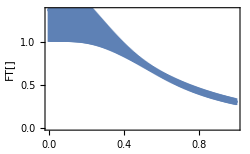
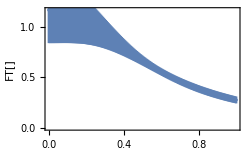
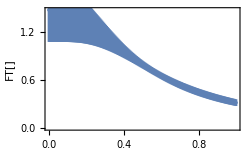
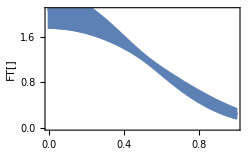
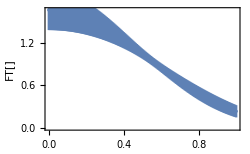
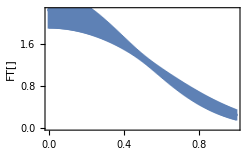
Simultaneous 4D fits for Re  for =-1
with 3 and 610
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Formula | FT Plot ()
Invariant: a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) Abs[P.b]) ⅇ^(-d b)
Cartesian: a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) Abs[b_L P_L]) ⅇ^(-d √(b_L^2+b_T^2)) | {a, c, k1, k2, d, f} | {⟨5.28(42)⟩_(2902J), ⟨0.51(12)⟩_(2902J), ⟨11.60(44)⟩_(2902J), ⟨-32.4(27)⟩_(2902J), ⟨0.580(13)⟩_(2902J), ⟨0.473(11)⟩_(2902J)} | 1.57561 | 357.058 | (a √(2/π) c ⅇ^(-d b))/(c^2+x^2) | -Graphics-
Invariant: a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) Abs[P.b]) ⅇ^(-d b^2)
Cartesian: a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) Abs[b_L P_L]) ⅇ^(-d (b_L^2+b_T^2)) | {a, c, k1, k2, d, f} | {⟨1.36(10)⟩_(2902J), ⟨0.53(13)⟩_(2902J), ⟨11.09(49)⟩_(2902J), ⟨-30.8(28)⟩_(2902J), ⟨0.0564(15)⟩_(2902J), ⟨0.473(12)⟩_(2902J)} | 4.38385 | 972.063 | (a √(2/π) c ⅇ^(-d b^2))/(c^2+x^2) | -Graphics-
Invariant: (a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) Abs[P.b]))/((1+d b^2)^j_2)
Cartesian: (a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) Abs[b_L P_L]))/((1+d (b_L^2+b_T^2))^j_2) | {a, c, k1, k2, d, f, j2} | {⟨3.53(47)⟩_(2902J), ⟨0.49(12)⟩_(2902J), ⟨11.79(45)⟩_(2902J), ⟨-33.0(26)⟩_(2902J), ⟨0.096(16)⟩_(2902J), ⟨0.473(11)⟩_(2902J), ⟨2.06(12)⟩_(2902J)} | 1.3183 | 301.388 | (a √(2/π) c)/((c^2+x^2) (1+d b^2)^j_2) | -Graphics-
Invariant: a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) (P.b)^2) ⅇ^(-d b)
Cartesian: a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) (b_L P_L)^2) ⅇ^(-d √(b_L^2+b_T^2)) | {a, c, k1, k2, d, f} | {⟨5.94(48)⟩_(2902J), ⟨0.114(30)⟩_(2902J), ⟨11.96(44)⟩_(2902J), ⟨-34.3(26)⟩_(2902J), ⟨0.588(14)⟩_(2902J), ⟨0.487(10)⟩_(2902J)} | 1.54574 | 350.516 | (a ⅇ^(-x^2/(4 c)) ⅇ^(-d b))/(√(2 c)) | -Graphics-
Invariant: a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) (P.b)^2) ⅇ^(-d b^2)
Cartesian: a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) (b_L P_L)^2) ⅇ^(-d (b_L^2+b_T^2)) | {a, c, k1, k2, d, f} | {⟨1.43(11)⟩_(2902J), ⟨0.122(33)⟩_(2902J), ⟨11.61(48)⟩_(2902J), ⟨-32.8(29)⟩_(2902J), ⟨0.0579(16)⟩_(2902J), ⟨0.483(12)⟩_(2902J)} | 4.58644 | 1016.43 | (a ⅇ^(-x^2/(4 c)) ⅇ^(-d b^2))/(√(2 c)) | -Graphics-
Invariant: (a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) (P.b)^2))/((1+d b^2)^j_2)
Cartesian: (a ⅇ^(-f η) ⅇ^(-c (1-k_1/η-k_2/η^2) (b_L P_L)^2))/((1+d (b_L^2+b_T^2))^j_2) | {a, c, k1, k2, d, f, j2} | {⟨3.68(38)⟩_(2902J), ⟨0.110(29)⟩_(2902J), ⟨12.02(44)⟩_(2902J), ⟨-34.8(26)⟩_(2902J), ⟨0.084(13)⟩_(2902J), ⟨0.4896(98)⟩_(2902J), ⟨2.16(14)⟩_(2902J)} | 1.35274 | 308.897 | (a ⅇ^(-x^2/(4 c)))/(√(2 c) (1+d b^2)^j_2) | -Graphics-

```mathematica
FitetarangeList[3,-1,6,10]
```

```mathematica
LorentzianFitList[bminForFit_,momL_]:=Module[{dataforfitA2B,fitJKA2B,fitParasA2B,stab, chiA2B,results={}},
Do[
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_}]:=a/(1+c*x2^2+d*x3^2)^2;
dataforfitA2B=Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->momL,bNum->even,etav->etaForFit}],{etav,bL,bT,data}],Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d}],{{a,5},{c,0.1},{d,0.001}},{n,bL,bT},modelfitA2B];
fitParasA2B=FitParameters/. fitJKA2B;
chiA2B=chisquareDoF/. fitJKA2B;
AppendTo[results,{etaForFit,OutputForm[fitParasA2B],chiA2B}];,{etaForFit,6,10}];
Print["Fit for Re  at fixed eta & =",momL,"\n","",bminForFit," are SELECTED for fit!\n Fit model:",modelfitA2B[,,,{a,c,d}],"\n",TableForm[results,TableHeadings->{None,{"η","Parameters {a, c, d}",""}},TableSpacing->{1,2}]];]
```

```mathematica
LorentzianFitList[3,-1]
```

Fit for Re  at fixed eta & =-1
3 are SELECTED for fit!
 Fit model:a/((1+c b_L^2+d b_T^2)^2)
η | Parameters {a, c, d} | 
6 | {⟨0.1697(67)⟩_(2902J), ⟨0.0807(29)⟩_(2902J), ⟨0.0844(34)⟩_(2902J)} | 0.421668
7 | {⟨0.149(11)⟩_(2902J), ⟨0.1101(60)⟩_(2902J), ⟨0.1145(71)⟩_(2902J)} | 0.30263
8 | {⟨0.151(22)⟩_(2902J), ⟨0.165(16)⟩_(2902J), ⟨0.173(19)⟩_(2902J)} | 0.51004
9 | {⟨0.149(44)⟩_(2902J), ⟨0.236(40)⟩_(2902J), ⟨0.240(48)⟩_(2902J)} | 0.984865
10 | {⟨0.15(24)⟩_(2902J), ⟨0.39(22)⟩_(2902J), ⟨0.40(25)⟩_(2902J)} | 1.22025

```mathematica
LorentzianFitList[bminForFit_,momL_,etamin_:6,etamax_:10]:=Module[{dataforfitA2B,fitJKA2B,fitParasA2B,chiA2B,results={},aVal,cVal,dVal},(*Global variables to store points with Jackknife samples*)cDataList={};
dDataList={};
Do[modelfitA2B[x1_,x2_,x3_,{a_,c_,d_}]:=a/(1+(c+d)*x2^2+d*x3^2)^2;
dataforfitA2B=Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->momL,bNum->even,etav->etaForFit}],{etav,bL,bT,data}],Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
If[Length[dataforfitA2B]>4,fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d}],{{a,0.1},{c,0.1},{d,0.09}},{n,bL,bT},modelfitA2B];
fitParasA2B=FitParameters/. fitJKA2B;
chiA2B=N[chisquareDoF/. fitJKA2B];
(*Store {eta,JackknifeSample} for plotting*)AppendTo[cDataList,{etaForFit,fitParasA2B[[2]]}];
AppendTo[dDataList,{etaForFit,fitParasA2B[[3]]}];
aVal=formatJK[fitParasA2B[[1]]];
cVal=formatJK[fitParasA2B[[2]]];
dVal=formatJK[fitParasA2B[[3]]];
AppendTo[results,{etaForFit,"{"<>aVal<>", "<>cVal<>", "<>dVal<>"}",NumberForm[chiA2B,{4,3}]}];];,{etaForFit,etamin,etamax}];
Print["Fit for Re \!\(\*SubscriptBox[OverscriptBox[\(A\), \(~\)], \(2 B\)]\) at fixed η (",etamin," ≤ η ≤ ",etamax,") & \!\(\*SubscriptBox[\(P\), \(L\)]\) = ",momL,"\nCut: |\!\(\*OverscriptBox[\(b\), \(⇀\)]\)| ≥ ",bminForFit,"a\n","Fit model: ",a/(1+(c+d)*Subsuperscript[b,L,2]+d*Subsuperscript[b,T,2])^2,"\n"];
TableForm[results,TableHeadings->{None,{"η","Parameters {a, c, d}","\!\(\*SuperscriptBox[\(χ\), \(2\)]\)/DoF"}},TableSpacing->{1,2}]];

(*Run the fits*)
LorentzianFitList[3,-1,6,10]
```

Fit for Re (Ã)_(2 B) at fixed η (6 ≤ η ≤ 10) & P_L = -1
Cut: |b⃗| ≥ 3a
Fit model: a/((1+(c+d) b_L^2+d b_T^2)^2)

η | Parameters {a, c, d} | χ^2/DoF
6 | {0.170(7), -0.004(2), 0.084(3)} | 0.422
7 | {0.149(10), -0.004(3), 0.114(7)} | 0.303
8 | {0.151(21), -0.008(7), 0.173(19)} | 0.510
9 | {0.149(43), -0.004(13), 0.240(48)} | 0.985
10 | {0.147(238), -0.012(45), 0.397(245)} | 1.220

```mathematica
LorentzianFitList[bminForFit_,momL_,etamin_:6,etamax_:10,exportPath_:Automatic]:=Module[{dataforfitA2B,fitJKA2B,fitParasA2B,chiA2B,results={},cVal,dVal,cInit=0.1,dInit=0.05,tableDisplay,finalCard,saveFile},(*Global lists for subsequent plotting*)cDataList={};
dDataList={};
Do[(*Model with fixed a=4*)modelfitA2B[x1_,x2_,x3_,{c_,d_}]:=(4*Exp[-0.5*x1])/(1+(c+d)*x2^2+d*x3^2)^2;
dataforfitA2B=Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->momL,bNum->even,etav->etaForFit}],{etav,bL,bT,data}],Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
If[Length[dataforfitA2B]>4,(*Fast fit using warm-started initial parameters*)fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{c,d}],{{c,cInit},{d,dInit}},{n,bL,bT},modelfitA2B];
fitParasA2B=FitParameters/. fitJKA2B;
chiA2B=N[chisquareDoF/. fitJKA2B];
(*Update initial guess for the next eta slice for instant convergence*)cInit=Max[meanJK[fitParasA2B[[1]]],0.001];
dInit=Max[meanJK[fitParasA2B[[2]]],0.001];
(*Store {eta,JackknifeSample}*)AppendTo[cDataList,{etaForFit,fitParasA2B[[1]]}];
AppendTo[dDataList,{etaForFit,fitParasA2B[[2]]}];
cVal=formatJK[fitParasA2B[[1]]];
dVal=formatJK[fitParasA2B[[2]]];
AppendTo[results,{ToString[etaForFit],"{"<>cVal<>", "<>dVal<>"}",ToString[NumberForm[chiA2B,{4,3}]]}];];,{etaForFit,etamin,etamax}];
(*Construct Elegant Publication-Ready Table Card*)tableDisplay=Grid[Join[{{"η","Parameters {c, d}","\!\(\*SuperscriptBox[\(χ\), \(2\)]\)/DoF"}},results],Frame->All,FrameStyle->Directive[RGBColor[0.75,0.75,0.75],AbsoluteThickness[0.8]],Background->{None,{RGBColor[0.92,0.94,0.98],{White,RGBColor[0.98,0.98,0.98]}}},Alignment->{{Center,Center,Center},Center},ItemSize->{{4,18,10},1.8},Dividers->{All,{True,True,Table[False,{Length[results]-1}],True}}];
finalCard=Column[{Style["Fit for Re \!\(\*SubscriptBox[OverscriptBox[\(A\), \(~\)], \(2 B\)]\) at Fixed η ("<>ToString[etamin]<>" ≤ η ≤ "<>ToString[etamax]<>") & \!\(\*SubscriptBox[\(P\), \(L\)]\) = "<>ToString[momL],Bold,13,FontFamily->"Helvetica"],Style["Spatial Cut: |\!\(\*OverscriptBox[\(b\), \(⇀\)]\)| ≥ "<>ToString[bminForFit]<>"a   |   Model: (4 \!\(\*SuperscriptBox[\(ⅇ\), \(-0.5 η\)]\))/(1 + (c + d)\!\(\*SubsuperscriptBox[\(b\), \(L\), \(2\)]\) + d\!\(\*SubsuperscriptBox[\(b\), \(T\), \(2\)]\)\!\(\*SuperscriptBox[\()\), \(2\)]\)",Italic,11,GrayLevel[0.3],FontFamily->"Helvetica"],Spacer[5],tableDisplay},Alignment->Center,Spacings->0.8];
(*Export to PDF*)saveFile=If[exportPath===Automatic,$HomeDirectory<>"/Lattice_QCD_TMD_PhD/Lattice-QCD-calculations-of-x-dependence-of-Sivers-TMD-Hariprashad-Ravikumar-NMSU-PhD-Thesis/Gaussian_type_fit_Real_A2B/LorentzianFixedA_P"<>ToString[momL]<>"_b"<>ToString[bminForFit]<>".pdf",exportPath];
Export[saveFile,finalCard,"PDF"];
Print["Exported neat table to: ",saveFile];
(*Display on screen*)finalCard];

(*Run the fits and export*)
LorentzianFitList[3,-1,6,10]
```

Fit for Re (Ã)_(2 B) at fixed η (6 ≤ η ≤ 10) & P_L = -1
Cut: |b⃗| ≥ 3a
Fit model: (4 ⅇ^(-0.5 η))/((1+(c+d) b_L^2+d b_T^2)^2)

η | Parameters {c, d} | χ^2/DoF
6 | {-0.005(2), 0.096(1)} | 0.925
7 | {-0.002(3), 0.097(2)} | 0.634
8 | {0.001(4), 0.100(3)} | 1.846
9 | {0.009(7), 0.099(4)} | 2.353
10 | {0.012(11), 0.102(6)} | 2.384

Saved publication plot to: /Users/hariprashadravikumar/Lattice_QCD_TMD_PhD/Lattice-QCD-calculations-of-x-dependence-of-Sivers-TMD-Hariprashad-Ravikumar-NMSU-PhD-Thesis/PowerLaw_etaAsymptotic/A2B_c_eta_AllAsymptoticModels_P1.pdf

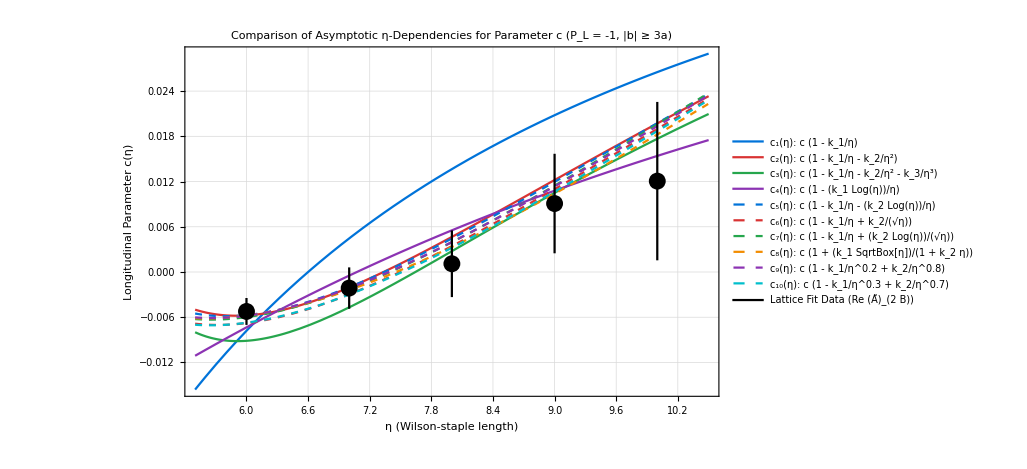

```mathematica
(*1. Define all candidate asymptotic models:Table models first (c1..c4),followed by other candidates (c5..c10)*)(*Table Models (Top of the list)*)c1[η_]:=0.078*(1-6.60/η);
c2[η_]:=0.146*(1-12.27/η-(-36.2)/η^2);
c3[η_]:=0.093*(1-6.7/η-36/η^2-(-220)/η^3);
c4[η_]:=0.092*(1-(3.616*Log[η])/η);

(*Other Asymptotic Candidates*)
c5[η_]:=0.240*(1-(-4.50)/η-(5.94*Log[η])/η);
c6[η_]:=0.43*(1-(-5.81)/η+(-4.86)/Sqrt[η]);
c7[η_]:=0.81*(1-0.409/η+(-1.284*Log[η])/Sqrt[η]);
c8[η_]:=0.59*(1+(-0.855*Sqrt[η])/(1+0.179*η));
c9[η_]:=1.18*(1-1.896/η^0.2+1.342/η^0.8);
c10[η_]:=0.90*(1-2.965/η^0.3+2.54/η^0.7);


(*2. Plot all continuous theoretical curves*)
plotCurvesAll=Plot[{c1[η],c2[η],c3[η],c4[η],c5[η],c6[η],c7[η],c8[η],c9[η],c10[η]},{η,5.5,10.5},PlotStyle->{{Thick,RGBColor[0.0,0.45,0.85]},(*c1:Blue*){Thick,RGBColor[0.85,0.20,0.20]},(*c2:Red*){Thick,RGBColor[0.15,0.65,0.30]},(*c3:Green*){Thick,RGBColor[0.55,0.20,0.70]},(*c4:Purple*){Thick,Dashed,RGBColor[0.0,0.45,0.85]},(*c5:Dashed Blue*){Thick,Dashed,RGBColor[0.85,0.20,0.20]},(*c6:Dashed Red*){Thick,Dashed,RGBColor[0.15,0.65,0.30]},(*c7:Dashed Green*){Thick,Dashed,RGBColor[0.95,0.55,0.00]},(*c8:Dashed Orange*){Thick,Dashed,RGBColor[0.55,0.20,0.70]},(*c9:Dashed Purple*){Thick,Dashed,RGBColor[0.00,0.75,0.80]}   (*c10:Dashed Cyan*)},PlotRange->All];


(*3. Plot lattice data points with Jackknife error bars from cDataList*)
plotDataC=ErrorListPlot[MakeErrBars[cDataList],PlotStyle->{Directive[Black,PointSize[0.016]]},PlotRange->All];


(*4. Combine into final figure with complete equation-based legend*)
finalPlotAll=Legended[Show[plotCurvesAll,plotDataC,PlotRange->All,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Dashed],FrameLabel->{Style["η (Wilson-staple length)",Bold,12,FontFamily->"Helvetica"],Style["Longitudinal Parameter c(η)",Bold,12,FontFamily->"Helvetica"]},PlotLabel->Style["Comparison of Asymptotic η-Dependencies for Parameter c (P_L = -1, |b| ≥ 3a)",Bold,13,FontFamily->"Helvetica"],ImageSize->760],Placed[LineLegend[{RGBColor[0.0,0.45,0.85],RGBColor[0.85,0.20,0.20],RGBColor[0.15,0.65,0.30],RGBColor[0.55,0.20,0.70],Directive[Dashed,RGBColor[0.0,0.45,0.85]],Directive[Dashed,RGBColor[0.85,0.20,0.20]],Directive[Dashed,RGBColor[0.15,0.65,0.30]],Directive[Dashed,RGBColor[0.95,0.55,0.00]],Directive[Dashed,RGBColor[0.55,0.20,0.70]],Directive[Dashed,RGBColor[0.00,0.75,0.80]],Black},{"\!\(\*SubscriptBox[\(c\), \(1\)]\)(η): c (1 - \!\(\*FractionBox[\(k_1\), \(η\)]\))","\!\(\*SubscriptBox[\(c\), \(2\)]\)(η): c (1 - \!\(\*FractionBox[\(k_1\), \(η\)]\) - \!\(\*FractionBox[\(k_2\), SuperscriptBox[\(η\), \(2\)]]\))","\!\(\*SubscriptBox[\(c\), \(3\)]\)(η): c (1 - \!\(\*FractionBox[\(k_1\), \(η\)]\) - \!\(\*FractionBox[\(k_2\), SuperscriptBox[\(η\), \(2\)]]\) - \!\(\*FractionBox[\(k_3\), SuperscriptBox[\(η\), \(3\)]]\))","\!\(\*SubscriptBox[\(c\), \(4\)]\)(η): c (1 - \!\(\*FractionBox[\(k_1 Log(η)\), \(η\)]\))","\!\(\*SubscriptBox[\(c\), \(5\)]\)(η): c (1 - \!\(\*FractionBox[\(k_1\), \(η\)]\) - \!\(\*FractionBox[\(k_2 Log(η)\), \(η\)]\))","\!\(\*SubscriptBox[\(c\), \(6\)]\)(η): c (1 - \!\(\*FractionBox[\(k_1\), \(η\)]\) + \!\(\*FractionBox[\(k_2\), \(\*SqrtBox[\(η\)]\)]\))","\!\(\*SubscriptBox[\(c\), \(7\)]\)(η): c (1 - \!\(\*FractionBox[\(k_1\), \(η\)]\) + \!\(\*FractionBox[\(k_2 Log(η)\), \(\*SqrtBox[\(η\)]\)]\))","\!\(\*SubscriptBox[\(c\), \(8\)]\)(η): c (1 + \!\(\*FractionBox[\(k_1 \*SqrtBox[\(η\)]\), \(1 + k_2 η\)]\))","\!\(\*SubscriptBox[\(c\), \(9\)]\)(η): c (1 - \!\(\*FractionBox[\(k_1\), SuperscriptBox[\(η\), \(0.2\)]]\) + \!\(\*FractionBox[\(k_2\), SuperscriptBox[\(η\), \(0.8\)]]\))","\!\(\*SubscriptBox[\(c\), \(10\)]\)(η): c (1 - \!\(\*FractionBox[\(k_1\), SuperscriptBox[\(η\), \(0.3\)]]\) + \!\(\*FractionBox[\(k_2\), SuperscriptBox[\(η\), \(0.7\)]]\))","Lattice Fit Data (Re \!\(\*SubscriptBox[OverscriptBox[\(A\), \(~\)], \(2 B\)]\))"},LegendFunction->"Frame",LegendLayout->{"Column",1},LabelStyle->{FontFamily->"Helvetica",FontSize->10}],Right]];


(*5. Export directly to Thesis folder*)
exportFile=$HomeDirectory<>"/Lattice_QCD_TMD_PhD/Lattice-QCD-calculations-of-x-dependence-of-Sivers-TMD-Hariprashad-Ravikumar-NMSU-PhD-Thesis/PowerLaw_etaAsymptotic/A2B_c_eta_AllAsymptoticModels_P1.pdf";
Export[exportFile,finalPlotAll,"PDF"];
Print["Saved publication plot to: ",exportFile];

(*Display on screen*)
finalPlotAll
```

Saved Table PDF to: /Users/hariprashadravikumar/Lattice_QCD_TMD_PhD/Lattice-QCD-calculations-of-x-dependence-of-Sivers-TMD-Hariprashad-Ravikumar-NMSU-PhD-Thesis/Gaussian_type_fit_Real_A2B/LorentzianFixedA_P-1_b3.pdf

Fit for Re (Ã)_(2 B) at Fixed η (6 ≤ η ≤ 10) & P_L = -1
Spatial Cut: |b⃗| ≥ 3a   |   Model: (4 ⅇ^(-0.5 η))/(1 + (c + d)b_L^2 + db_T^2)^2

η | Parameters {c, d} | χ^2/DoF
6 | {-0.0052(18), 0.0964(13)} | 0.925
7 | {-0.0021(27), 0.0967(17)} | 0.634
8 | {0.0011(44), 0.1001(25)} | 1.846
9 | {0.0091(66), 0.0987(36)} | 2.353
10 | {0.0121(105), 0.1016(57)} | 2.384

Saved c(η) plot to: /Users/hariprashadravikumar/Lattice_QCD_TMD_PhD/Lattice-QCD-calculations-of-x-dependence-of-Sivers-TMD-Hariprashad-Ravikumar-NMSU-PhD-Thesis/PowerLaw_etaAsymptotic/A2B_c_eta_AllAsymptoticModels_P1.pdf

-Graphics-

Saved d(η) plot to: /Users/hariprashadravikumar/Lattice_QCD_TMD_PhD/Lattice-QCD-calculations-of-x-dependence-of-Sivers-TMD-Hariprashad-Ravikumar-NMSU-PhD-Thesis/PowerLaw_etaAsymptotic/A2B_d_eta_Independence_P1.pdf

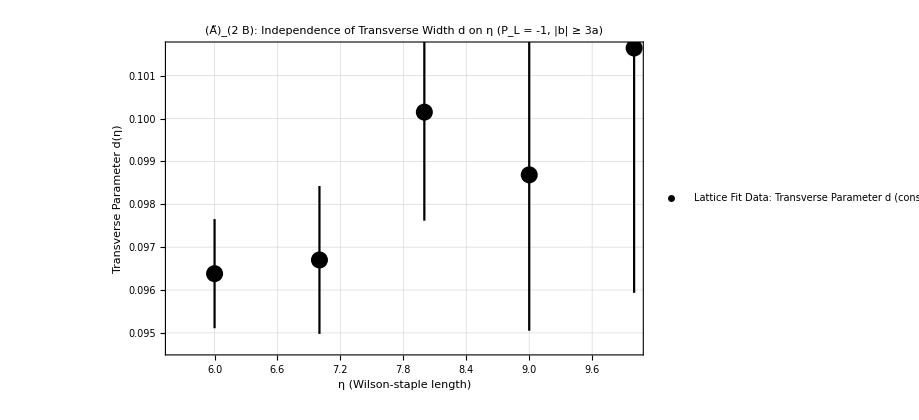

```mathematica
(* =========================================================================*)(*0. Helper Functions for Jackknife Mean,Error& Formatting*)(* =========================================================================*)meanJK[jk_]:=MakeErrBars[{{1,jk}}][[1,1,2]];
errJK[jk_]:=MakeErrBars[{{1,jk}}][[1,2,1,2]];
formatJK[jk_]:=ToString[NumberForm[meanJK[jk],{4,4}]]<>"("<>ToString[Round[10000*errJK[jk]]]<>")";

(* =========================================================================*)
(*1. Unified Fitting Routine for Fixed a=4 at each η Slice*)
(* =========================================================================*)
RunLorentzianFits[bminForFit_,momL_,etamin_:6,etamax_:10]:=Module[{dataforfitA2B,fitJKA2B,fitParasA2B,chiA2B,results={},cVal,dVal,cInit=0.1,dInit=0.05,tableDisplay,finalCard,saveFile},cDataList={};
dDataList={};
Do[modelfitA2B[x1_,x2_,x3_,{c_,d_}]:=(4*Exp[-0.5*x1])/(1+(c+d)*x2^2+d*x3^2)^2;
dataforfitA2B=Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->momL,bNum->even,etav->etaForFit}],{etav,bL,bT,data}],Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
If[Length[dataforfitA2B]>4,fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{c,d}],{{c,cInit},{d,dInit}},{n,bL,bT},modelfitA2B];
fitParasA2B=FitParameters/. fitJKA2B;
chiA2B=N[chisquareDoF/. fitJKA2B];
cInit=Max[meanJK[fitParasA2B[[1]]],0.001];
dInit=Max[meanJK[fitParasA2B[[2]]],0.001];
AppendTo[cDataList,{etaForFit,fitParasA2B[[1]]}];
AppendTo[dDataList,{etaForFit,fitParasA2B[[2]]}];
cVal=formatJK[fitParasA2B[[1]]];
dVal=formatJK[fitParasA2B[[2]]];
AppendTo[results,{ToString[etaForFit],"{"<>cVal<>", "<>dVal<>"}",ToString[NumberForm[chiA2B,{4,3}]]}];];,{etaForFit,etamin,etamax}];
(*Table Card*)tableDisplay=Grid[Join[{{"η","Parameters {c, d}","\!\(\*SuperscriptBox[\(χ\), \(2\)]\)/DoF"}},results],Frame->All,FrameStyle->Directive[RGBColor[0.75,0.75,0.75],AbsoluteThickness[0.8]],Background->{None,{RGBColor[0.92,0.94,0.98],{White,RGBColor[0.98,0.98,0.98]}}},Alignment->{{Center,Center,Center},Center},ItemSize->{{4,18,10},1.8}];
finalCard=Column[{Style["Fit for Re \!\(\*SubscriptBox[OverscriptBox[\(A\), \(~\)], \(2 B\)]\) at Fixed η ("<>ToString[etamin]<>" ≤ η ≤ "<>ToString[etamax]<>") & \!\(\*SubscriptBox[\(P\), \(L\)]\) = "<>ToString[momL],Bold,13,FontFamily->"Helvetica"],Style["Spatial Cut: |\!\(\*OverscriptBox[\(b\), \(⇀\)]\)| ≥ "<>ToString[bminForFit]<>"a   |   Model: (4 \!\(\*SuperscriptBox[\(ⅇ\), \(-0.5 η\)]\))/(1 + (c + d)\!\(\*SubsuperscriptBox[\(b\), \(L\), \(2\)]\) + d\!\(\*SubsuperscriptBox[\(b\), \(T\), \(2\)]\)\!\(\*SuperscriptBox[\()\), \(2\)]\)",Italic,11,GrayLevel[0.3],FontFamily->"Helvetica"],Spacer[5],tableDisplay},Alignment->Center,Spacings->0.8];
saveFile=$HomeDirectory<>"/Lattice_QCD_TMD_PhD/Lattice-QCD-calculations-of-x-dependence-of-Sivers-TMD-Hariprashad-Ravikumar-NMSU-PhD-Thesis/Gaussian_type_fit_Real_A2B/LorentzianFixedA_P"<>ToString[momL]<>"_b"<>ToString[bminForFit]<>".pdf";
Export[saveFile,finalCard,"PDF"];
Print["Saved Table PDF to: ",saveFile];
finalCard];

(*Run the fits*)
RunLorentzianFits[3,-1,6,10]


(* =========================================================================*)
(*2. Plot c(η) with All Asymptotic Models (No Clipping)*)
(* =========================================================================*)
(*Asymptotic model definitions*)
c1[η_]:=0.078*(1-6.60/η);
c2[η_]:=0.146*(1-12.27/η-(-36.2)/η^2);
c3[η_]:=0.093*(1-6.7/η-36/η^2-(-220)/η^3);
c4[η_]:=0.092*(1-(3.616*Log[η])/η);
c5[η_]:=0.240*(1-(-4.50)/η-(5.94*Log[η])/η);
c6[η_]:=0.43*(1-(-5.81)/η+(-4.86)/Sqrt[η]);
c7[η_]:=0.81*(1-0.409/η+(-1.284*Log[η])/Sqrt[η]);
c8[η_]:=0.59*(1+(-0.855*Sqrt[η])/(1+0.179*η));
c9[η_]:=1.18*(1-1.896/η^0.2+1.342/η^0.8);
c10[η_]:=0.90*(1-2.965/η^0.3+2.54/η^0.7);

plotCurvesAll=Plot[{c1[η],c2[η],c3[η],c4[η],c5[η],c6[η],c7[η],c8[η],c9[η],c10[η]},{η,5.5,10.5},PlotStyle->{{Thick,RGBColor[0.0,0.45,0.85]},{Thick,RGBColor[0.85,0.20,0.20]},{Thick,RGBColor[0.15,0.65,0.30]},{Thick,RGBColor[0.55,0.20,0.70]},{Thick,Dashed,RGBColor[0.0,0.45,0.85]},{Thick,Dashed,RGBColor[0.85,0.20,0.20]},{Thick,Dashed,RGBColor[0.15,0.65,0.30]},{Thick,Dashed,RGBColor[0.95,0.55,0.00]},{Thick,Dashed,RGBColor[0.55,0.20,0.70]},{Thick,Dashed,RGBColor[0.00,0.75,0.80]}},PlotRange->All];

plotDataC=ErrorListPlot[MakeErrBars[cDataList],PlotStyle->{Directive[Black,PointSize[0.016]]},PlotRange->All];

finalPlotC=Legended[Show[plotCurvesAll,plotDataC,PlotRange->All,PlotRangePadding->{{Scaled[0.05],Scaled[0.05]},{Scaled[0.15],Scaled[0.15]}},(*Prevents error bar clipping*)Frame->True,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Dashed],FrameLabel->{Style["η (Wilson-staple length)",Bold,12,FontFamily->"Helvetica"],Style["Longitudinal Parameter c(η)",Bold,12,FontFamily->"Helvetica"]},PlotLabel->Style["Comparison of Asymptotic η-Dependencies for Parameter c (P_L = -1, |b| ≥ 3a)",Bold,13,FontFamily->"Helvetica"],ImageSize->760],Placed[LineLegend[{RGBColor[0.0,0.45,0.85],RGBColor[0.85,0.20,0.20],RGBColor[0.15,0.65,0.30],RGBColor[0.55,0.20,0.70],Directive[Dashed,RGBColor[0.0,0.45,0.85]],Directive[Dashed,RGBColor[0.85,0.20,0.20]],Directive[Dashed,RGBColor[0.15,0.65,0.30]],Directive[Dashed,RGBColor[0.95,0.55,0.00]],Directive[Dashed,RGBColor[0.55,0.20,0.70]],Directive[Dashed,RGBColor[0.00,0.75,0.80]],Black},{"\!\(\*SubscriptBox[\(c\), \(1\)]\)(η): c (1 - \!\(\*FractionBox[\(k_1\), \(η\)]\))","\!\(\*SubscriptBox[\(c\), \(2\)]\)(η): c (1 - \!\(\*FractionBox[\(k_1\), \(η\)]\) - \!\(\*FractionBox[\(k_2\), SuperscriptBox[\(η\), \(2\)]]\))","\!\(\*SubscriptBox[\(c\), \(3\)]\)(η): c (1 - \!\(\*FractionBox[\(k_1\), \(η\)]\) - \!\(\*FractionBox[\(k_2\), SuperscriptBox[\(η\), \(2\)]]\) - \!\(\*FractionBox[\(k_3\), SuperscriptBox[\(η\), \(3\)]]\))","\!\(\*SubscriptBox[\(c\), \(4\)]\)(η): c (1 - \!\(\*FractionBox[\(k_1 Log(η)\), \(η\)]\))","\!\(\*SubscriptBox[\(c\), \(5\)]\)(η): c (1 - \!\(\*FractionBox[\(k_1\), \(η\)]\) - \!\(\*FractionBox[\(k_2 Log(η)\), \(η\)]\))","\!\(\*SubscriptBox[\(c\), \(6\)]\)(η): c (1 - \!\(\*FractionBox[\(k_1\), \(η\)]\) + \!\(\*FractionBox[\(k_2\), \(\*SqrtBox[\(η\)]\)]\))","\!\(\*SubscriptBox[\(c\), \(7\)]\)(η): c (1 - \!\(\*FractionBox[\(k_1\), \(η\)]\) + \!\(\*FractionBox[\(k_2 Log(η)\), \(\*SqrtBox[\(η\)]\)]\))","\!\(\*SubscriptBox[\(c\), \(8\)]\)(η): c (1 + \!\(\*FractionBox[\(k_1 \*SqrtBox[\(η\)]\), \(1 + k_2 η\)]\))","\!\(\*SubscriptBox[\(c\), \(9\)]\)(η): c (1 - \!\(\*FractionBox[\(k_1\), SuperscriptBox[\(η\), \(0.2\)]]\) + \!\(\*FractionBox[\(k_2\), SuperscriptBox[\(η\), \(0.8\)]]\))","\!\(\*SubscriptBox[\(c\), \(10\)]\)(η): c (1 - \!\(\*FractionBox[\(k_1\), SuperscriptBox[\(η\), \(0.3\)]]\) + \!\(\*FractionBox[\(k_2\), SuperscriptBox[\(η\), \(0.7\)]]\))","Lattice Fit Data (Re \!\(\*SubscriptBox[OverscriptBox[\(A\), \(~\)], \(2 B\)]\))"},LegendFunction->"Frame",LegendLayout->{"Column",1},LabelStyle->{FontFamily->"Helvetica",FontSize->10}],Right]];

exportFileC=$HomeDirectory<>"/Lattice_QCD_TMD_PhD/Lattice-QCD-calculations-of-x-dependence-of-Sivers-TMD-Hariprashad-Ravikumar-NMSU-PhD-Thesis/PowerLaw_etaAsymptotic/A2B_c_eta_AllAsymptoticModels_P1.pdf";
Export[exportFileC,finalPlotC,"PDF"];
Print["Saved c(η) plot to: ",exportFileC];
finalPlotC


(* =========================================================================*)
(*3. Plot d(η) Showing Independence on η (No Error Bar Clipping)*)
(* =========================================================================*)
finalPlotD=Legended[ErrorListPlot[MakeErrBars[dDataList],PlotStyle->{Directive[Black,PointSize[0.018]]},PlotRange->All,PlotRangePadding->{{Scaled[0.08],Scaled[0.08]},{Scaled[0.20],Scaled[0.20]}},(*Full headroom for error bars*)Frame->True,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Dashed],FrameLabel->{Style["η (Wilson-staple length)",Bold,12,FontFamily->"Helvetica"],Style["Transverse Parameter d(η)",Bold,12,FontFamily->"Helvetica"]},PlotLabel->Style["\!\(\*SubscriptBox[OverscriptBox[\(A\), \(~\)], \(2 B\)]\): Independence of Transverse Width d on η (P_L = -1, |b| ≥ 3a)",Bold,13,FontFamily->"Helvetica"],ImageSize->680],Placed[PointLegend[{Black},{"Lattice Fit Data: Transverse Parameter d (constant across η)"},LegendFunction->"Frame",LegendLayout->{"Column",1},LabelStyle->{FontFamily->"Helvetica",FontSize->11}],Top]];

exportFileD=$HomeDirectory<>"/Lattice_QCD_TMD_PhD/Lattice-QCD-calculations-of-x-dependence-of-Sivers-TMD-Hariprashad-Ravikumar-NMSU-PhD-Thesis/PowerLaw_etaAsymptotic/A2B_d_eta_Independence_P1.pdf";
Export[exportFileD,finalPlotD,"PDF"];
Print["Saved d(η) plot to: ",exportFileD];
finalPlotD
```

Saved Table PDF to: /Users/hariprashadravikumar/Lattice_QCD_TMD_PhD/Lattice-QCD-calculations-of-x-dependence-of-Sivers-TMD-Hariprashad-Ravikumar-NMSU-PhD-Thesis/Gaussian_type_fit_Real_A2B/LorentzianFixed_ImA2B_P-1_b3.pdf

Fit for Im (Ã)_(2 B) at Fixed η (6 ≤ η ≤ 10) & P_L = -1
Spatial Cut: |b⃗| ≥ 3a   |   Model: (0.267 b_L ⅇ^(-0.4702 η))/(1 + (c + d)b_L^2 + db_T^2)^1.108

η | Parameters {c, d} | χ^2/DoF
6 | {0.0129(407), 0.3277(358)} | 2.033
7 | {0.0521(585), 0.3059(470)} | 1.938
8 | {0.0671(1104), 0.3346(840)} | 1.252
9 | {0.2724(1536), 0.2536(987)} | 1.040
10 | {0.6084(2810), 0.1409(1084)} | 0.645

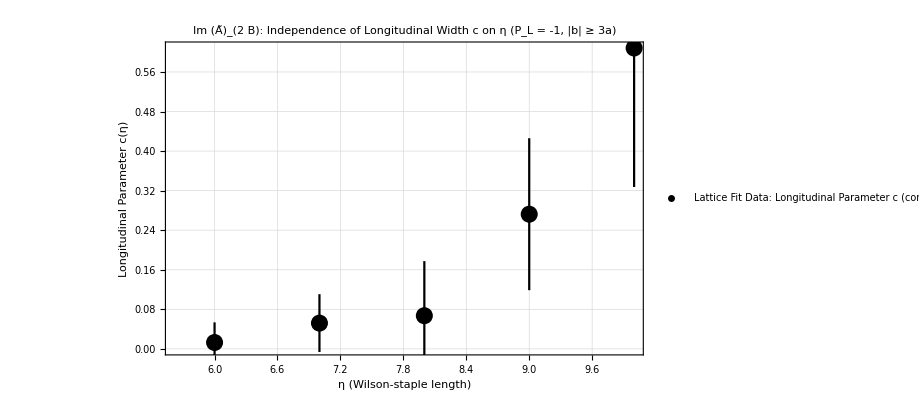

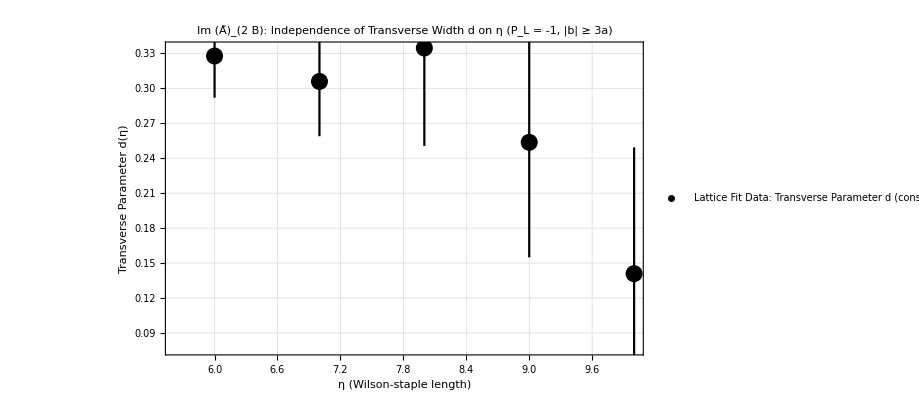

Saved Table PDF to: /Users/hariprashadravikumar/Lattice_QCD_TMD_PhD/Lattice-QCD-calculations-of-x-dependence-of-Sivers-TMD-Hariprashad-Ravikumar-NMSU-PhD-Thesis/Gaussian_type_fit_Real_A2B/LorentzianFixed_ReA12B_P-1_b3.pdf

Fit for Re (Ã)_(12 B) at Fixed η (6 ≤ η ≤ 10) & P_L = -1
Spatial Cut: |b⃗| ≥ 3a   |   Model: (-0.658 ⅇ^(-0.4702 η))/(1 + (c + d)b_L^2 + db_T^2)^2.0054

η | Parameters {c, d} | χ^2/DoF
6 | {0.0236(169), 0.0730(56)} | 0.604
7 | {0.0388(288), 0.0728(77)} | 0.860
8 | {0.0174(424), 0.0799(127)} | 0.831
9 | {-0.0105(575), 0.0925(214)} | 0.730
10 | {-0.0723(871), 0.1230(479)} | 0.468

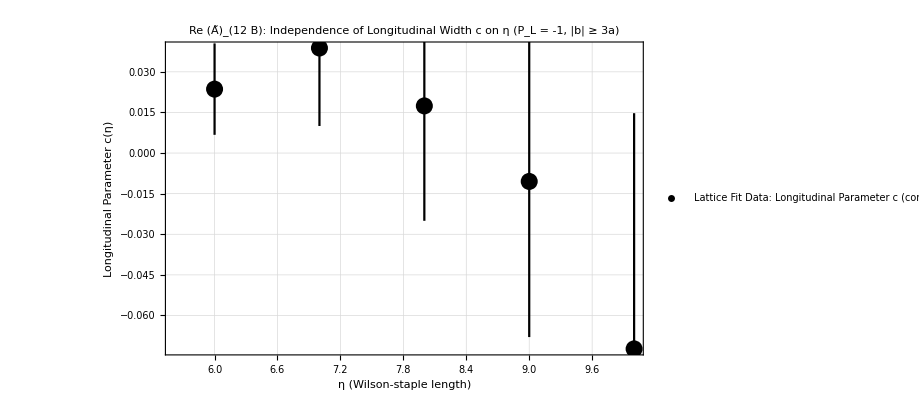

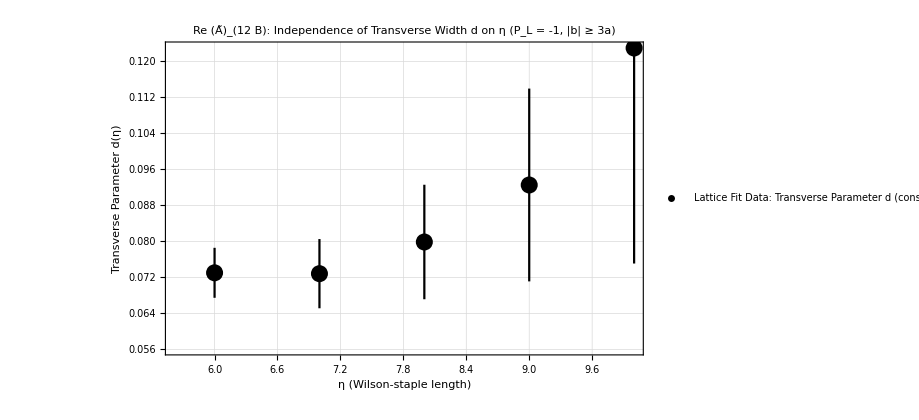

```mathematica
(* =========================================================================*)(*0. Helper Functions for Jackknife Mean,Error& Formatting*)(* =========================================================================*)meanJK[jk_]:=MakeErrBars[{{1,jk}}][[1,1,2]];
errJK[jk_]:=MakeErrBars[{{1,jk}}][[1,2,1,2]];
formatJK[jk_]:=ToString[NumberForm[meanJK[jk],{4,4}]]<>"("<>ToString[Round[10000*errJK[jk]]]<>")";


(* =========================================================================*)
(*1. Unified Fitting Routine for Im A2B (Fixed a=0.267,f=0.4702,j=1.108)*)
(* =========================================================================*)
RunLorentzianFitsImA2B[bminForFit_,momL_,etamin_:6,etamax_:10]:=Module[{dataforfitImA2B,fitJKImA2B,fitParasImA2B,chiImA2B,results={},cVal,dVal,cInit=0.22,dInit=0.22,tableDisplay,finalCard,saveFile},cDataListImA2B={};
dDataListImA2B={};
Do[modelfitImA2B[x1_,x2_,x3_,{c_,d_}]:=(0.267*x2*Exp[-0.4702*x1])/(1+(c+d)*x2^2+d*x3^2)^1.108;
dataforfitImA2B=Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->momL,bNum->odd,etav->etaForFit}],{etav,bL,bT,data}],Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
If[Length[dataforfitImA2B]>4,fitJKImA2B=JackknifeFit4D[dataforfitImA2B,modelfitImA2B[n,bL,bT,{c,d}],{{c,cInit},{d,dInit}},{n,bL,bT},modelfitImA2B];
fitParasImA2B=FitParameters/. fitJKImA2B;
chiImA2B=N[chisquareDoF/. fitJKImA2B];
(*Warm-start initials for next slice*)cInit=Max[meanJK[fitParasImA2B[[1]]],0.001];
dInit=Max[meanJK[fitParasImA2B[[2]]],0.001];
AppendTo[cDataListImA2B,{etaForFit,fitParasImA2B[[1]]}];
AppendTo[dDataListImA2B,{etaForFit,fitParasImA2B[[2]]}];
cVal=formatJK[fitParasImA2B[[1]]];
dVal=formatJK[fitParasImA2B[[2]]];
AppendTo[results,{ToString[etaForFit],"{"<>cVal<>", "<>dVal<>"}",ToString[NumberForm[chiImA2B,{4,3}]]}];];,{etaForFit,etamin,etamax}];
(*Table Card*)tableDisplay=Grid[Join[{{"η","Parameters {c, d}","\!\(\*SuperscriptBox[\(χ\), \(2\)]\)/DoF"}},results],Frame->All,FrameStyle->Directive[RGBColor[0.75,0.75,0.75],AbsoluteThickness[0.8]],Background->{None,{RGBColor[0.92,0.94,0.98],{White,RGBColor[0.98,0.98,0.98]}}},Alignment->{{Center,Center,Center},Center},ItemSize->{{4,18,10},1.8}];
finalCard=Column[{Style["Fit for Im \!\(\*SubscriptBox[OverscriptBox[\(A\), \(~\)], \(2 B\)]\) at Fixed η ("<>ToString[etamin]<>" ≤ η ≤ "<>ToString[etamax]<>") & \!\(\*SubscriptBox[\(P\), \(L\)]\) = "<>ToString[momL],Bold,13,FontFamily->"Helvetica"],Style["Spatial Cut: |\!\(\*OverscriptBox[\(b\), \(⇀\)]\)| ≥ "<>ToString[bminForFit]<>"a   |   Model: (0.267 \!\(\*SubscriptBox[\(b\), \(L\)]\) \!\(\*SuperscriptBox[\(ⅇ\), \(-0.4702 η\)]\))/(1 + (c + d)\!\(\*SubsuperscriptBox[\(b\), \(L\), \(2\)]\) + d\!\(\*SubsuperscriptBox[\(b\), \(T\), \(2\)]\)\!\(\*SuperscriptBox[\()\), \(1.108\)]\)",Italic,11,GrayLevel[0.3],FontFamily->"Helvetica"],Spacer[5],tableDisplay},Alignment->Center,Spacings->0.8];
saveFile=$HomeDirectory<>"/Lattice_QCD_TMD_PhD/Lattice-QCD-calculations-of-x-dependence-of-Sivers-TMD-Hariprashad-Ravikumar-NMSU-PhD-Thesis/Gaussian_type_fit_Real_A2B/LorentzianFixed_ImA2B_P"<>ToString[momL]<>"_b"<>ToString[bminForFit]<>".pdf";
Export[saveFile,finalCard,"PDF"];
Print["Saved Table PDF to: ",saveFile];
finalCard];

(*Run the fits*)
RunLorentzianFitsImA2B[3,-1,6,10]


(* =========================================================================*)
(*2. Plot c(η) and d(η) for ImA2B (Independence Plots)*)
(* =========================================================================*)

finalPlotCImA2B=Legended[ErrorListPlot[MakeErrBars[cDataListImA2B],PlotStyle->{Directive[Black,PointSize[0.018]]},PlotRange->All,PlotRangePadding->{{Scaled[0.08],Scaled[0.08]},{Scaled[0.20],Scaled[0.20]}},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Dashed],FrameLabel->{Style["η (Wilson-staple length)",Bold,12,FontFamily->"Helvetica"],Style["Longitudinal Parameter c(η)",Bold,12,FontFamily->"Helvetica"]},PlotLabel->Style["Im \!\(\*SubscriptBox[OverscriptBox[\(A\), \(~\)], \(2 B\)]\): Independence of Longitudinal Width c on η (P_L = -1, |b| ≥ 3a)",Bold,13,FontFamily->"Helvetica"],ImageSize->680],Placed[PointLegend[{Black},{"Lattice Fit Data: Longitudinal Parameter c (constant across η)"},LegendFunction->"Frame",LegendLayout->{"Column",1},LabelStyle->{FontFamily->"Helvetica",FontSize->11}],Top]];

exportFileCImA2B=$HomeDirectory<>"/Lattice_QCD_TMD_PhD/Lattice-QCD-calculations-of-x-dependence-of-Sivers-TMD-Hariprashad-Ravikumar-NMSU-PhD-Thesis/PowerLaw_etaAsymptotic/ImA2B_c_eta_Independence_P1.pdf";
Export[exportFileCImA2B,finalPlotCImA2B,"PDF"];
Print[finalPlotCImA2B];


finalPlotDImA2B=Legended[ErrorListPlot[MakeErrBars[dDataListImA2B],PlotStyle->{Directive[Black,PointSize[0.018]]},PlotRange->All,PlotRangePadding->{{Scaled[0.08],Scaled[0.08]},{Scaled[0.20],Scaled[0.20]}},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Dashed],FrameLabel->{Style["η (Wilson-staple length)",Bold,12,FontFamily->"Helvetica"],Style["Transverse Parameter d(η)",Bold,12,FontFamily->"Helvetica"]},PlotLabel->Style["Im \!\(\*SubscriptBox[OverscriptBox[\(A\), \(~\)], \(2 B\)]\): Independence of Transverse Width d on η (P_L = -1, |b| ≥ 3a)",Bold,13,FontFamily->"Helvetica"],ImageSize->680],Placed[PointLegend[{Black},{"Lattice Fit Data: Transverse Parameter d (constant across η)"},LegendFunction->"Frame",LegendLayout->{"Column",1},LabelStyle->{FontFamily->"Helvetica",FontSize->11}],Top]];

exportFileDImA2B=$HomeDirectory<>"/Lattice_QCD_TMD_PhD/Lattice-QCD-calculations-of-x-dependence-of-Sivers-TMD-Hariprashad-Ravikumar-NMSU-PhD-Thesis/PowerLaw_etaAsymptotic/ImA2B_d_eta_Independence_P1.pdf";
Export[exportFileDImA2B,finalPlotDImA2B,"PDF"];
Print[finalPlotDImA2B];


(* =========================================================================*)
(*3. Unified Fitting Routine for Re A12B (Fixed a=0.658,f=0.4702,j=2.0054)*)
(* =========================================================================*)
RunLorentzianFitsReA12B[bminForFit_,momL_,etamin_:6,etamax_:10]:=Module[{dataforfitReA12B,fitJKReA12B,fitParasReA12B,chiReA12B,results={},cVal,dVal,cInit=0.07,dInit=0.07,tableDisplay,finalCard,saveFile},cDataListReA12B={};
dDataListReA12B={};
Do[modelfitReA12B[x1_,x2_,x3_,{c_,d_}]:=(-0.658*Exp[-0.4702*x1])/(1+(c+d)*x2^2+d*x3^2)^2.0054;
dataforfitReA12B=Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->momL,bNum->even,etav->etaForFit}],{etav,bL,bT,data}],Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
If[Length[dataforfitReA12B]>4,fitJKReA12B=JackknifeFit4D[dataforfitReA12B,modelfitReA12B[n,bL,bT,{c,d}],{{c,cInit},{d,dInit}},{n,bL,bT},modelfitReA12B];
fitParasReA12B=FitParameters/. fitJKReA12B;
chiReA12B=N[chisquareDoF/. fitJKReA12B];
cInit=Max[meanJK[fitParasReA12B[[1]]],0.001];
dInit=Max[meanJK[fitParasReA12B[[2]]],0.001];
AppendTo[cDataListReA12B,{etaForFit,fitParasReA12B[[1]]}];
AppendTo[dDataListReA12B,{etaForFit,fitParasReA12B[[2]]}];
cVal=formatJK[fitParasReA12B[[1]]];
dVal=formatJK[fitParasReA12B[[2]]];
AppendTo[results,{ToString[etaForFit],"{"<>cVal<>", "<>dVal<>"}",ToString[NumberForm[chiReA12B,{4,3}]]}];];,{etaForFit,etamin,etamax}];
(*Table Card*)tableDisplay=Grid[Join[{{"η","Parameters {c, d}","\!\(\*SuperscriptBox[\(χ\), \(2\)]\)/DoF"}},results],Frame->All,FrameStyle->Directive[RGBColor[0.75,0.75,0.75],AbsoluteThickness[0.8]],Background->{None,{RGBColor[0.92,0.94,0.98],{White,RGBColor[0.98,0.98,0.98]}}},Alignment->{{Center,Center,Center},Center},ItemSize->{{4,18,10},1.8}];
finalCard=Column[{Style["Fit for Re \!\(\*SubscriptBox[OverscriptBox[\(A\), \(~\)], \(12 B\)]\) at Fixed η ("<>ToString[etamin]<>" ≤ η ≤ "<>ToString[etamax]<>") & \!\(\*SubscriptBox[\(P\), \(L\)]\) = "<>ToString[momL],Bold,13,FontFamily->"Helvetica"],Style["Spatial Cut: |\!\(\*OverscriptBox[\(b\), \(⇀\)]\)| ≥ "<>ToString[bminForFit]<>"a   |   Model: (-0.658 \!\(\*SuperscriptBox[\(ⅇ\), \(-0.4702 η\)]\))/(1 + (c + d)\!\(\*SubsuperscriptBox[\(b\), \(L\), \(2\)]\) + d\!\(\*SubsuperscriptBox[\(b\), \(T\), \(2\)]\)\!\(\*SuperscriptBox[\()\), \(2.0054\)]\)",Italic,11,GrayLevel[0.3],FontFamily->"Helvetica"],Spacer[5],tableDisplay},Alignment->Center,Spacings->0.8];
saveFile=$HomeDirectory<>"/Lattice_QCD_TMD_PhD/Lattice-QCD-calculations-of-x-dependence-of-Sivers-TMD-Hariprashad-Ravikumar-NMSU-PhD-Thesis/Gaussian_type_fit_Real_A2B/LorentzianFixed_ReA12B_P"<>ToString[momL]<>"_b"<>ToString[bminForFit]<>".pdf";
Export[saveFile,finalCard,"PDF"];
Print["Saved Table PDF to: ",saveFile];
finalCard];

(*Run the fits*)
RunLorentzianFitsReA12B[3,-1,6,10]


(* =========================================================================*)
(*4. Plot c(η) and d(η) for ReA12B (Independence Plots)*)
(* =========================================================================*)

finalPlotCReA12B=Legended[ErrorListPlot[MakeErrBars[cDataListReA12B],PlotStyle->{Directive[Black,PointSize[0.018]]},PlotRange->All,PlotRangePadding->{{Scaled[0.08],Scaled[0.08]},{Scaled[0.20],Scaled[0.20]}},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Dashed],FrameLabel->{Style["η (Wilson-staple length)",Bold,12,FontFamily->"Helvetica"],Style["Longitudinal Parameter c(η)",Bold,12,FontFamily->"Helvetica"]},PlotLabel->Style["Re \!\(\*SubscriptBox[OverscriptBox[\(A\), \(~\)], \(12 B\)]\): Independence of Longitudinal Width c on η (P_L = -1, |b| ≥ 3a)",Bold,13,FontFamily->"Helvetica"],ImageSize->680],Placed[PointLegend[{Black},{"Lattice Fit Data: Longitudinal Parameter c (constant across η)"},LegendFunction->"Frame",LegendLayout->{"Column",1},LabelStyle->{FontFamily->"Helvetica",FontSize->11}],Top]];

exportFileCReA12B=$HomeDirectory<>"/Lattice_QCD_TMD_PhD/Lattice-QCD-calculations-of-x-dependence-of-Sivers-TMD-Hariprashad-Ravikumar-NMSU-PhD-Thesis/PowerLaw_etaAsymptotic/ReA12B_c_eta_Independence_P1.pdf";
Export[exportFileCReA12B,finalPlotCReA12B,"PDF"];
Print[finalPlotCReA12B];


finalPlotDReA12B=Legended[ErrorListPlot[MakeErrBars[dDataListReA12B],PlotStyle->{Directive[Black,PointSize[0.018]]},PlotRange->All,PlotRangePadding->{{Scaled[0.08],Scaled[0.08]},{Scaled[0.20],Scaled[0.20]}},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Dashed],FrameLabel->{Style["η (Wilson-staple length)",Bold,12,FontFamily->"Helvetica"],Style["Transverse Parameter d(η)",Bold,12,FontFamily->"Helvetica"]},PlotLabel->Style["Re \!\(\*SubscriptBox[OverscriptBox[\(A\), \(~\)], \(12 B\)]\): Independence of Transverse Width d on η (P_L = -1, |b| ≥ 3a)",Bold,13,FontFamily->"Helvetica"],ImageSize->680],Placed[PointLegend[{Black},{"Lattice Fit Data: Transverse Parameter d (constant across η)"},LegendFunction->"Frame",LegendLayout->{"Column",1},LabelStyle->{FontFamily->"Helvetica",FontSize->11}],Top]];

exportFileDReA12B=$HomeDirectory<>"/Lattice_QCD_TMD_PhD/Lattice-QCD-calculations-of-x-dependence-of-Sivers-TMD-Hariprashad-Ravikumar-NMSU-PhD-Thesis/PowerLaw_etaAsymptotic/ReA12B_d_eta_Independence_P1.pdf";
Export[exportFileDReA12B,finalPlotDReA12B,"PDF"];
Print[finalPlotDReA12B];
```